```mathematica
importDir ="/home/gillen/Documents/Computation/saved_outputs/2D_Cartesian_allbcs/Twist:90-45/Date:19-Oct-2015 23:53:23/";
nMatrix= Import[importDir<>"nMatrix.mat"]⟦1⟧;
avgEnergy = Import[importDir <> "aveEnergy.mat"]⟦1⟧;
Dimensions@nMatrix;


(*nMatrix=Transpose[nMatrix,{1,4,2,3}];*)
```

```mathematica
nMatrix=Transpose[nMatrix,{1,4,2,3}];
{frames,X,Y}=Dimensions[nMatrix]⟦;;-2⟧
θMatrix=ArcTan[nMatrix⟦;;,;;,;;,1⟧,nMatrix⟦;;,;;,;;,2⟧];
```

{50,10,10}

```mathematica
(*Manipulate[ListVectorPlot[nMatrix⟦frame,;;,;;⟧,VectorStyle-> Blue,VectorPoints->All],{frame,1,frames,1}]*)
```

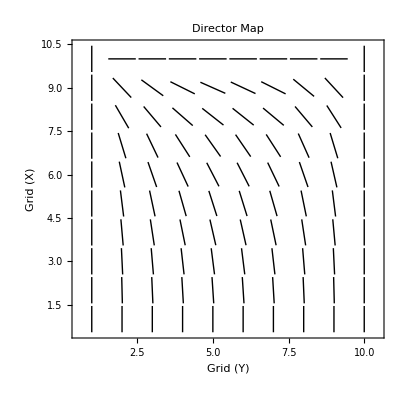

```mathematica
(*Manipulate[ListDensityPlot[Sin[θMatrix⟦frame⟧]^2 ᵀ,ColorFunctionScaling->False,ColorFunction->GrayLevel],{frame,1,frames,1}]*)
ListVectorPlot[nMatrix⟦50,;;,;;⟧,VectorStyle-> Arrowheads[0],VectorPoints->All, PlotTheme->"Monochrome", FrameLabel->{"Grid (Y)" ,"Grid (X)"},PlotLabel->"Director Map" ]
```

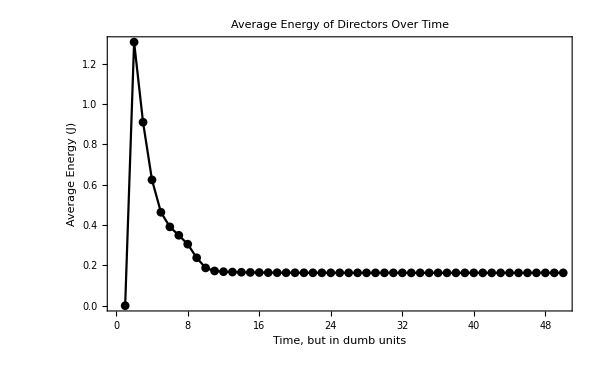

```mathematica
ListPlot[avgEnergy, PlotRange->All,PlotTheme->"Monochrome",PlotMarkers->Automatic,Joined->True,InterpolationOrder->1,Frame->True, Axes->True, FrameLabel->{"Time, but in dumb units","Average Energy (J)"}, PlotLabel->"Average Energy of Directors Over Time"]
```

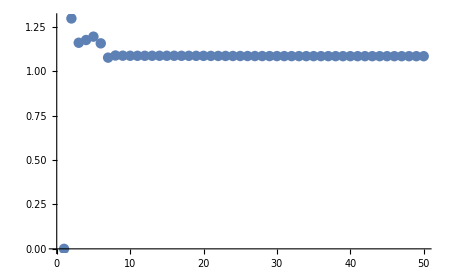

{{0.,1.30703,0.909564,0.62384,0.463276,0.390825,0.349084,0.304975,0.23757,0.187248,0.172237,0.168503,0.16686,0.165759,0.164954,0.164368,0.163946,0.163644,0.16343,0.163278,0.163168,0.163088,0.163028,0.162982,0.162947,0.162919,0.162896,0.162878,0.162863,0.16285,0.16284,0.162831,0.162824,0.162818,0.162813,0.162809,0.162805,0.162802,0.1628,0.162798,0.162796,0.162794,0.162793,0.162792,0.162791,0.162791,0.16279,0.16279,0.162789,0.162789}}

{50,10,10,2}

```mathematica
ListPlot[{0.,1.2965761061742789,1.1598023488870153,1.175175211348111,1.194206914453935,1.156482330919994,1.076011731887819,1.088086218563446,1.0870596625087101,1.0865999677531708,1.0863953280048886,1.0864144761650822,1.0865187783514767,1.0865908918821618,1.0865913237932483,1.0865277681747068,1.086419425144511,1.0862826756702963,1.0861295329366771,1.0859694190600566,1.0858088786198992,1.0856527851539253,1.0855042861550421,1.0853657932359448,1.085238162373206,1.0851215601946615,1.085016063786419,1.084920991843714,1.0848355318847587,1.0847590974054513,1.0846907683360467,1.0846297610480138,1.0845752774961244,1.0845267740404458,1.084483565161948,1.084445051034703,1.0844108256487517,1.0843803900181,1.084353309613212,1.0843292881548598,1.0843079651924856,1.084289026746915,1.0842722566283556,1.0842573949341976,1.0842442307400055,1.0842325617527413,1.0842222474718717,1.084213121884689,1.084205041137634,1.0841979050128812}, PlotRange->All]
```

```mathematica
[ـ.00.00.00.00.00.00.01IM.0f.00.00.00/.00.00.00x.1c㣠`p.00b6 怒 
峢a.10?$3758$5.00.13ʿ3㥟$.03{.00}Ĉ}.0f.00.00.00,.00.00.00x.1c㣠`0.00b6 怒 
峢a.10?/478$5 .18.05.01	A@.1d.01.01.00Dg.04/.0f.00.00.00*.00.00.00x.1c㣠`0.00b6 怒 
峢a.10\ZQbnj1.03.03.13PĈȇ.00:.14.03$.0f.00.00.006.00.00.00x.1c㣠`ࢶ 怒 
峂1.13.14.06㓳r
3+R9.01l.01 裫.0f/v0.1a.00淏>.0f.00.00.00+.00.00.00x.1c㣠`0.00b6 怒 
峂1.13CJ.05.03.03'T|W%凬.00:1.05.15.0f.00.00.00+.00.00.00x.1c㣠`0.00b6 怒 
峂1.13CJ%.03.03'T|W%凬.00:D.05.16.0f.00.00.002.00.00.00x.1c㣠`.18.01Ĭ@́%A.00.15ʧ.02bF .0c.00Ҍ@.1c.02⳱3021sprю.05r.07.00G⏀.00.00>.00.00.00x.1c=΁.0e.00@.08CQD.07Yx?NIȿ$i:㱳_	%;˨=:.07冣ą.01.04ↂ뮃Ï.00.00.00+.00.00.00x.1c㣠`0.00b6 怒 
峂13.037!!.03'T\꾑Ǵ䕶.006g.04ڏ.00.00.00+.00.00.00x.1c㣠`0.00b6 怒 
峂13.037.11.11.03'T|jJ僺?Sm.01:m.05Ϗ.00.00.00+.00.00.00x.1c㣠`0.00b6 怒 
峂13.03711.03'T\꾑Ǵ䕶.0061.04ޏ.00.00.00..00.00.00x.1c㣠`p.00b6 怒 
峢a.10Xzbnn".10愊W.0b,s.7fX5Ş.00Zֆ^.0f.00.00.00o.04.00.00x.1c5һPԕ.14.07僑ÈQ(AC.117">q4嬈ꈒA"R.19.04u.05.15T(1.10.05.06.11啀ƃa.17.1a.04 y.08!{.00X.10x̒ϥ!;00.0f;.04ʋ"m4:d95d9߹w9贚.05%4.1arіў憎2.1aʬ.7f.19㕥Ԕ	鐦8M]9g剧*.0bҰ풢nƁ֨y.06-#.10.13쫇ы0.19.17.1aǽ2.18+ʴ.0eߘ+Ĉ8м.116&W..1dϾ.1c.0e/z.07&J.02-Ⱪ].01cWb.19V韖ÃU(͊3:7.05.0336ᢅp#8;.15Uh/味(#.14#/۬.1d.17N	Xޥxݳb.04Z@.1dެ-٦矈Ϟӫ.0f㍤폝$	߷hx,ҠaԦ;ۓ;밞.16軆N.15.14.0f頹
؍.0b:9Ï
.౧㺬.066켳8);.03.0b焻Z7t Ӊ0W	6㽘.>وo0.0c.1ej.04s)^5ヴj.1e6\<.P1㣷
C.ߔ.0f洟
p뇆vʪ蕽8ކ.02^.1cW柽k	.1cь䙷}.1d~kǌ&SAib/Ҧ,?t..1d.98P뻅
a<{᠍1.14a\1.12ޔR?.04.Y>쟴{0(휞Z};ś5ؙ͔.19D.05V:BTlRߩȚŇ媥b|ě˝M.16#Ρ1Hu]1zی1'丁m<<1`.08ⵐI,K.04ѱ%ƗBǰD%
̀.17Rd-4	.11.Ã.0b.1ea.9a)N剚>Rtʎެ8C.0c.1aყg,E.14庿.0eꨭi]  ㈩4Y.02.1e.18!.133I`-*d晡ᑔ@.14.02@bE˖.01߉\^ؾ`!<'͒5s.14s/zŁ&.1e伵Y.1d1".02vG]tMډ.1c
!盛`8샂f+ܟ撠.10G
.00Q.02;݆z=
.0bc!O.08|o.1e4MT@ ޸著I Ω愢֬3.0fw 08饔#.048.076.07d.16.12В[s뉐Ջ0bٺ*߷'q+7~F@眼gX.0e9陲毲鰼+칽rТ'?箼.0f%.1fϑ4P=.0cG.03o.0e.17.01.15.11է'}堻.18ڼ.16!.03Ỵ.17:d9b6y݇Rh첉0xG.06ֻ.03:*펽hbGꅓ<*9캺޿r
.0c|.0c쥐.1ab.1e.1c.139.0e.1a2؝̪q伂y.1f.04lɗW.0f.05ˀylc쌵.1c⥵&>͞.11.00ٹ3m.1d"1d쯹R.12*.02=[O!l=mѽ+R.08.1e׬.05|
.11橶.1d.15
!h/j牅;/Bۻ+a.14,T刱쪀".02sT.03齠Z.14.14펿8.10>N.12G.00^.07ĵ92!.0c=,$χϞ.05nb.0f.00.00.00.13.00.00.00x.1c㣠`X.00Ĭ@́%A.00.15ʷ.02bF(.06볒.0b
3똀씰晌)L.06̿.19O2LeMdӣ죒g.1c.17.16箃<}<Q|j牴	.06	)	?.17ޭҮ.1a,&/넳$?.144㩍2➲ⲏ巨Ԩz(	(?P^#R!ꢦ .0er.0f.00.1d.19"D.0f.00.00.00*.00.00.00x.1c㣠`0.00b6 怒 
峢av .΋,ȫͥ`.02
.18.03遲*.0f.00.00.00'.00.00.00x.1c㣠`0.00b6 怒 
峂1.13Cf&.03.03.0b.10.16Pg`.00.00.1c .01t.0f.00.00.00v.00.00.00x.1c㣠`.08`f``.03Ҝ.0c.10.1a.04X!|.(fd`fp頠.042.15.00ꗘ~u໷f.1fզa.11.18ӫ퉬7r.10ۥ7觫ތ.03鄤>3.1e1.13.06л&@ĭ8.0et.02ԭ+
Ԃ鳣_:d90eݨy#捧ц_׏.00.00.00'.01.00.00x.1c㣠`8.08.00.06$9.18 4.080B醣(͉ĉe鮹)E镐u 1	@I>.0f6?ֽ~n/f:.Ɂ+6.07.13꺢1e.1f.0fثi1.15$^>l?˯),3:dbbb.1c)k.0c.0fۯZ+{KMོ#	!.0c<.07ퟲ\4Mg9l.1f役迃绔c:de64￝ǳůC뼊.1cT.7f.1e2g.1f֧Ƹ㐽겟.0fٛx~ˎM'5.17h$.00陓xž}9d_l筐橺.14	$/鉙.01i.1e_"ۘ.01乾	;.1f.0fٟ.1dfxj.0f.10鼔y.11.10.1e.7fcߦn ĥ.10>꼪&.10>!rmi.0c.10.16ﺓ.08$쫽끤/><㈤3.1c^JY.03韩.07.1f.19.02鴘׎C .1d峝 ݲa>.16.10.1e+Y.12!.01$.05'>5Q.03ҏ.00iƲS.0cʀ:㊀ڤ遲
 uF&/䁴։.19& Zꤜ9 Ͱk'.1c.08>.11巕.16H.03.00n+ӹ.0f.00.00.00-.00.00.00x.1c㣠`0.00b6 怒 
峂1.13.14.06㋲S
3+R.19.00"\\.0c.0c.00Br.03폀.00.00Z.00.00.00x.1c퉁	.000.10DёPDD.10tb.1f9YAnz	"9X.02%Z.0e+&.06O෗t;)6m:daf2:+͍胕}ᭋ9Ű.1d겿4.'.00.00.00.00.00.00.00?x.00.0cɂ.0f.00.00.00)À.00x.1cԘy4.15}ׇ
厉4.08ʐ9.15.10"D톔w.12.1a.15$
n	e(.15.05ʔ*c.19.12*.11.152Vې!SƸ.1cÁ9μ5.08.10=癷;޿.1e뽿z.1ew-瞫:dd6du֙.1f5Ͼ篳GHH(f.1d0.10.18๋.10㦊RF.10.12┓$0 %.05麋s縺8{89y
	.0b>;6NX迫>6N.1aҟ౒.03$Ꚃ*\*.1c>1 嫅.0b絼8'&tQ*.17@MƦ)w.11r.0cKyX5&:da68o.1a"﹉ぃ~鬌V5俐.01/.1f䩙ᘪ.1e.1c}.13Ɂ.19╙4ᢐ볾įU?n.0c緧ݖ>急.02
|.0en-.1f.b96.1a/,Z	ܭ載:ʞꔩ߅_
M&Ĉ뙘5uȪď&)>+.0f.17
;.(m/ܽÙ.0eř᪲yl8dl.1d%5ʀ.1f.0b.03/战.1cx1A..0f.14זc31.hx࠷&.02T_ǆ0c
Ϲش* &Q	.07O¿D?Ȫ.04=%.0e.1d3䁽Ҫkͷ.02Z.14.13.7f_ā	)I篖7Q︞]/7.0eī.0cޛ걉.00㗹vg.0eΡꕧ.1c.04>ȿ3.7fn{.08.0b"k.02:df85୬4.18B).(R.1d.1cߩۊᆁ㲲=h0=04ਐ湚ɢC.01.04帚3e取h3б֚.19ʌ"̉X誼.07.14~Z.07:dd2f%է%1+Ћ.17.0eᘸt荐_81Zs.13^֏.15ϒ}.0e搠_;qS$+.0b<>/l.10傓>҇.15-䳸+>㿶컟Ԭ.07KΉw➹.17.1f.X椊.af.05.17.0eՅt.00𝕜7.0b7.17.00St.02(쬵j.08ԉ]s>챬	g.1aឮ
ܞ.1d.13;PɃ9Yղmᦊ]fՇ.0b.1c$.16gf1btL+Ψ.05Ӿ,O.0b2堚8.01-hk	.17.1c.02+.067ҏ[3ѐ췘.ŝ䍒.18?ࢍ.1e.=2=T~N'<.14S,.16.1d.1c.89گ5.0b'.07I<Uց.16*sy႟=z.18担-.15N!CF&*.1d.0c8#.1e[䔼.14냩:^ǋ0쵓.1e&녦R.1f.15࿳ƲJfU.195.14zc3.11]pX:޽㪮٨1.08̏z⪿-.13:=)֯Ũ賛8Gூ\C.0b.1fi<
ϧTco윭.0f8(.12ز`.135.11.1cZ>zPӚ w.07ꬶ.0b.1e̋$鉆.85.15͟//硇똟ĳ	n.O	ࢎ偳3.190轥.VX.13.04- b(n.04P욼6ɌÚM3п
쪇?Dj^OڠE.10Ꚗ޵>.0cw̷k_.11<.1f.03.0f*.1a>ב(.17-.1cܵjᇔ.19n>6㸢l.1e컼XD=.07".02.0e|迸.07븤8.0b.0c.03.1d.14.02.17ɖӕ.17sᢗ>͓oC .1eZu!ƈɏ7r+*0ٷ\ګӁ̮.1d2b1jHuѾ%޸37.1a뷶.18ֻ"bګW.07=ۑĠ/u褍~.12aꩇ풬H)J-ެL.00[ꞯ[6.0e.11x>⟭?攠.0bÊ.15.074.&첌.0c.17桷>>ߥ!.1f:d9cfP٨쒷qi+.0fR̆f?n⣮$鹵.0bä޽1ꢛ1.16.1cY뤩1DÍk&ٖe.040ʣ.0f(
ਏ}㭘.04ğ*=7γ1db.1dk.0b.0f.01i?բMB.18$^ɰVᗟ믶1.11.07.01;.0cO~%
.13 x0.0ev%VΡ@㏍.0b.05Ё妾.02.13k.0cr2:Ɥ⭫Oެ~.07.1a.11Q
.13.02፨컉 峤ӧeꎑ쑰>.17.1fЮ87'ߥ.1e.10Щ滚.12ܿ˯^?]s.08.04.08.11;9r.1eޱ
⮝K.03'.1cn.07쵝￶.1f.06+NKl^?}.10.0bS.03ï$vᦿN夽ߨ	a(ثu?U 7}.1a1$6.0bǧYMe119oeԋ.1a.01ҋÀﾕiϼ.07mo2 P.1a>0ď㏎;ֹ.1dY.05P7-.1d#噋ࠐO谱5::d94e@.03.04.06⇜*4.14뼡K8Ҽ9ɯu$닩(.15.04*ྕ.05*贒|㪓.16᦯{͂y>̔ส谎O귀║/.12.0fԠ.ț3.03j.18$^)l}.0b.15@٪'wڡT<.11=/8跮М}䛇1.07o.05lfd8Ґh옿
n.07ګ=.1ezѭet.12ﳞź/s.07Pnރ}.03Alp=z1=<.1eAq~T%㶮8
.7f-1>˂+&	즑.01<+MU|*X
?뗯`.160H濫㞎(.04ǉո,$ ꚙ.14hIF౧㯞.06.04游.04.1e`!".06퓴 /k+h$.1e=㹺펰:dfd83⢈"!퓓pڱ嵍f&ܡ	֩v.12p83/9Z.11.0fƎb☦o@e|a.12xM.1eY+c#ʐ4堎(Mܜ谎F.17.03!":d815&6: .18
Ŗ.015U!,,3.14.0c}2.08.07쇂ȧqwKуv:(̺8B_4.0b=k.17.0c$I೪L~G&
kO	.19:
壷ן.1c.07.129(kĳ+3.18.04%^-.03&rϟο.16kވ3!2Еz.15e@ݻ.08fY*ȍầS.1d-.0c0kW^.19ꎍ.1f;mZaY.1d![n-.0b.17<2壕%YQ)Rw坼Ykص㬈S6?{".00Ɗ׵7|x	ţ.16A䝤.16<ːq;_+ХᏯ.07Ⱥw.搿.1eBNۺ錂䯄Z8pp.15&$r.0bR?8Ntr⵹8ޙM@辑RG.1eښR"='8$޴ڏm#w徽л.1e
먕3ڮ೰):dc68.03.1d#o.1a4\e@.16{.03iq]TXٶ.16"Q&㞐ﯼe?_jᢂ6.19y.0bq>.16$.067Nߌ.07.0e.0e9Ӗ.16.1dHۿśi]'̟vޤ9:.04.0b54◗ϣṝ亸-7bO.7fgCo.05;㖾.07朋t.0c+ȹ;.15C.03i螗;\.18n63\ٔ.0e	6)휂.16|\թ/LL㾺.10ԍ 3Lૺ
鍊szOᗄYī.1dA.1c'ѕ师.1f'䩴	.02VɆ43[눺oe7>L.1dF.033.1d6.1fb2	䊅n.1c)䢏2
ⅈ~찗*eT.0eА.0bE/WKy8R ֺ">їO⽕ዘ&ġ.04.03fᦷ7.04<ꏡ.17pP㪍Ȕ.03t<KqkQ.0b.1c:p$깿.1f.12.1d와?Ǧ石I<Э.19Ks+	(ؚ6k.0f`/嘌ꮡ.00e.1ayˎO@ĩ띻O.10P.14.14?礊A|쁽tś.01^.14.15ܞ.132.7f\>w抎Ĭᑿ㥸/ûr靾(ͺg-.1a&xO.18y4ӆ].00.03#r.102C公\*.1fIϬ#槦.15쾒.02)	卫280晉ń~'876l8Xǃ3즫㲆.18|^x
9M`@.1770:d9c8.0f.1e!c.7f<.14$φՂ|冮8ܛ<-.7f^.13&֧.04/맀C.14*y3A0/oK.01
ڤ@*.16.13oМXL.17.02.169ꔓ.0b噪.17Ϭ.1e丏:$56v.14.0f#ݱDⶬ_<ӱ.14B.05	.0343.1e.12.187DS瘄冬q2.7fحR.18N뜿	,U).04𝒪pl.1c.1c尛5_-h(#걶.01.05<.1fՖ].19^Դ.17.1fr;̓%?.0bl.1ciJ︯\.15.11P6l꭫#T.0e/%©?.0c)x&E쯸.18.0e.06荺Ʉ.06lڼB.05*n߳❏tĝ7;;4㦤䧆͸ꈥa쪱鹖.0b/;CK3.174 鷳5.07p?2葝ͰLQe
^紹).hUzч%.02ਐ쾵Gr:⫋V:9PGP
+棵$ϙ*.0b.03N[w㋜-1>]5H⍸.b
G٘飔9.01g.16-.08^.17.85052w.18B= .12Pr.1fߟ.0f粌G.1d>.10.0b.08뉩ǩɒE1.0bɻ.02픋=@Iζsj.92.16ɘY
`Oq<.7fr^☺칺H֩̒5'.01移뙠Gm]8ﶪ7|>Ժ.08ї.1a0:.1e@-.05ҙ.18%|u۳.05>,.1e.1d!lͪƞ9.05;'.1e.0c.01p$2O·.03ߟ39.0e3v1V4.08:/ㆋ
ힱ43213#䵋ð.06.07zjF.07wʶ.02t.11엌e/:df09~4♂a
Ѱ>.18阸Aܱ۪g$0#곖.18G.16ZTV˯隂Pmi3Ε.023E.19޶:de38.0cQjyIﵪ	o.199.1fe垜KN!p.02=ፕ#m8e߫1	U.02罖縔.04߂瓿Ｋ㜥澔.07.7f)^m>.07Ru{Q"ꄴj.0e.1f.96<R{z.00
2.b2.12#
|ȧ.1eՙ犃.12ߍ詏'承iР_=~D0'vŉ.08ֈ--9.04.046oî.10p.0c:.14.0f:db0315ϱ,L>.14%.146ޓ`.11x?'Wk.17*.0f1gj.06G].10,.19%.02폋.040).17쎜(ԡ@E嶝7"2A{жLl?.07.16.0f轾6l.18Ļ4.08.1aa%ʅY9K.16頻.19ih3.1f.0eT-韂=@1s݁ƯٗԇƋZk
.0f.0f.0fU-.0bŃ.03夞.19ᑻE.16.0c>ꥍ>	,{'.12K.03.13.0f.1eMx.0eqЙ'tyZ!.1fB&-.16߼Ǆ)㉬.03﹐.ۨs䗄.0b?%W*ˢC.17.03C$w.13.10沼f.04 .00=TM
.1d䞷[.1e]E.01;fש.05
.04暍JJЦ@ઑEg9Q.06.08߷62ֽ.0cg꯴.13(ŶSZ)'/
"5.15[㦨	㰙X.15>׺Xl~
.0b:d9f3ݢ:dd3f/;:.0b.00M	f2хm:df478.11&镄.0f;6}.1aڜԀ
;셽uz<v྆?.1d.7fH蔵
X痊Ӈ;",.05襡].04.1d.17-ऐ.07.01ϴ.18.1d粁"2ͱDZ.152E]=_/+'յ':\ƅ*.10
Z|.0b7j.1crk.18z.03n#.7fl.089
084{_.11.7f76Ep⹠.1eT.18.01A:鵜䞂eM.0e⚣z묉d.17.1f.13等.0f5.14ยT.17.15iEݔ恉.1d寨Ʊ߷+۪{I<֕Sѝ5͐5̹ш压s.0eښ⛖^k.07મc+V.08.18횮p青-.11= %葜.1cG⅔F.1d8ͫƘ.01.82˂㜈澮+gf"Ӈ3T.17.1f
4.19ą 1	3.04ꙉg24诲.18l'䯶ٽ.1ah.02z恦缒㒩1&Ե7Ы.1?jӘ.10-1B.0f?҃J.16앣#.03.10f٤iX@紶ۙҋ.14|ʝ:g.0b[0.0f		ݶ.0c"!EVeѫ
.16>捖.03
>8.0e.1f.13"0@#Ĵ{΀j+.1co2lꦩ:d9df-!!2Ǹ#.1e렆
/!㻻ĸ).1f%..147箓ソꩥ*	%
.18骭c㟯꼇
K;.07.01.02.07[.18p60.I	Ɂ.0f#畍)ð鏝쁽3r.15z=.0fI.00wϯM~.04,֚^r8.0b<.1fꞓ苖q-+녺1pʳ.1eE.1d.01.14.10W?.102.02&.19	.0e5C\p.17罾-.17>.12?˔|ϳO՟:N.11鉂/.0f".01<.18..13.1c.11Am.02(PӋm1C0u.05/3Kp.1f?s*R.0e.04ṗ申ʳ눱..1c.1f78P
,Ϧ6o:d99d졡.02R>TEk>.1d.06$摠.06*.1f2梁|ȩ
7]jҋͮ.0b҃.16.08捻Fѷ;)$޷ɵ⢂.7f0.n^.1f*.14.049%.02y爯սş8HǤwᑬx.19霰f-.13.11.11K䀕.197"ARd}&8't.1d뢃*i՚c{.02b.18Y氬쑑=b6\.0b.13.0bڠ6.08..01#Ӣn\.0cؓN5-ba`98.0bbe$얜p.18.07۵.1e=荁6{.U꭛֌.0b}.0e.18@П.12>n}W۞).04{'.15.03.141.16<ѵ8:ތ⏇$.04s⪱+G⼗.1f
о.19R4Ⱦ.05$gꘆYBkĮ쨇:3BҲ.04|S.1d>줓:%Ϟla=䑉.1e%c7ƾ.0cÿ.02.00.00藔Sݺ.06U

.16
џPT.10iJU臅%*U,⪶T.10.11頂 ".02RD:ȤH/B蝀.02	)K.10"4O補.0b=隻_㤙O>.19韁<ߺ.11ӄ銏Ѕ.0f.19)R쐛.1f/.10똱雏؞).00U帚ӆ3ᵙaתe.1fP	੿P.1d	}3ruB<.08.14.1aV.
-#".13鯗؆.18 .13.14v.02̛.0f.18.1f^.0eY.1a.0cึ":3gK	r9.1eR	b Wꝱr#脘.06D.1f!"C.19}՞%K噹.18(.16T倽K2g.0f6郱8漫.07æث)į(ւyѯl.04.1e>6
䍩.01Ϸʅᛒ
%汸.1a*tǈ".16├	.02㙤pٿ.08焓+㬱.14.18!쬇	圙r/㢒
⻒r*R*?i3.01ỳ.03.1aGQ.13Ri.14ˍN.1c/!앮y妨\;m,ǉD.11.0bU.15D.19.06贬햗.06.&Z~ȍ뀧킩Ҵ.10,G0.084Wc-ט8.1e䎗㻞Ԡ1'f}.15.1d.18깜.12*?㑯.1c.1d诞@A.0b.1d.17(HR@~ꊻ.19ݹ.18q嗈(a3ט鸘e|.12E.1c/r.14.0eg )Ř粘Ȍ.1aZ}ẅَ.16
v .0c݆&=s_u!+.05AK]/踞蟻짯.0f.1aV.0b.1dZ`ɩܵϽ.18ฮ,-9.0c^!.0e.1fꌰh5.1d㑦.00>.1fc.18|͐Ur$`.10%'Z鐃쉋RG.18.18ذj:ddd4Kˊf
.03㱑*>U.18.0c.04芵m'Aj朻6B+꡼ꅻ.1dȹЏ.06㝸VZ7ƢpX	*.0eZ0퓣I྾1	F.1e̖.172.1e?.10].18.17z$.02.1283ڸ㨠ȗ5ݩ.00.03ǻrR.9aٜ.03૶儉.0c"٣894h0+2.17캂.01;:֏.08.121.10>R欅E>J9}͛.03;".1d..0b.14.12.0e7b.1355.02.0eNNBQ|I.1d椽.7fC.01_;
3ډd7В$A3돵{Ȉù)j븕熭.0f0q<厈cP{a.14༓.06KL1l飽@܆8 _
Qp9k{N3Ჵﰇf.06zz|&䒏
T"e㸁Se&.1d迠..08މ.1a.04e6Q.00٪Aԣ夾-H.06:d9d1.06G֨\颰.01w%.15ܴݰ.1fǕ.0bե.19W(0: 㲤	.11vnϣj.1e끇97k+ɝܓɐͤ\҇䮁fդ.14.036荳켿߃.7fw蕚.13tx.17.0bP]殏
$ ;3.01/|k3жaۛƁ.1d.08Dﻄ%~.003K_׎~:d8beF<ὀכ.1fೝ+4.16.12jy.07j.0ba.0c;w_.bdXݿ.14M#Ѵ~.0f.17窯Ў攺:ND/.03t+I믻'Ԑ.0e
3N.0fk<.181vשGn
(.02.15Nⶴt;"ܖ禋밂/
	ֳߺf`1
ĪrÇ.05L8ٰ܎.1fҋԭ3큱.06.12ᐵˠu.06s癈t.14!r.02`恎ҹ.03楉w.02:da28)饁,.13D/>ⷚ.1e.046,6콼c.14Ǜg.9eT.16[.03.1c.05.1f'Z㑞+Y?.10✞:ddbfτ⹴붉t[9TGg.19.06܂R	w҈ȏ=9.b2k7.0e뭲.1a.1a.19.0b.16.19.13Ǎ].06.107$!ӿ#.19V.1a{m佇PԝH߹.05a丮b.07ᏻpI;$稷BI繕⎧@԰:ә
.E릏0цx=靪ڼ.11(?ЎDb#Ӝ.03?)ȜE8.16n6.0e.1cd)紦Ѐ.18鈑.11".
.0e.11ψ΋Ov.0eO"}.07.0cZ##.13h׎p#.05&ʕ7.0c9D&"Mv叜.1eaH}Չ6.05:da1e".1f糇#JK.1e\y.1c.04.1e娫G.7f`0הּɛ.00	C.03'tWX猂t£'u.18ЕT.02诔.19㱝.15i.1f.05.0c~1'Bw08I.1e.19w60l,.06^$G'.01*"Ч.08*!.0fO.17.19̄PկͽIt.1cϡ҆ٗo1.18k랝4.02ĥ^r挄?,틑! oR+f'7	XJ.175줛((.06.N.190.00X0Jk>
!.12/7jX禯.05΂3.18ܟآæ.0frㄷ&萔.1a¨t.08.1f.14.17щ'@}ѻQ.03־޶.1e#.0f
M⸊6\㬼֨&.1f*p鄻.015ݗ.12(0膾λ.08.0c:?>庬?
֭{5>r.0c#=#͊ۼŵ<.00?߉e.17.03ެ.7f93.1d.1a厧.03).1c.18,ʏ"!丠찚+ A4칅=.13=<౨5$.13ԃb;㦰<E.:da67.18.18Zˌ65.02Y:ꠐ̘.0c켏笖.06.02&?..1c׸.1d谭O녆ߥ=.0e.19.0b斉.0b.0f>#.bd.05.17಑Na{.07z,Gaݥ.11垎귝詔.16Jޫ+.1c-Akޔ”3Iځ@<.7fW♁3ݡ"V.17⡞$Ҿ.[.0bRm.19ڒ,䮀$۳乗5Eo+.04߻ڪ ;*W)(ӛL졿ޟRֽk"D.14.01+'.1dSۭ.016.04$ŧ.04.16#w1
.0c.00.06.104.1c␑樖+.13Pj U9 D@ݦ;Ⱗ(욹*.15-9.01.1cֱ鎗g.02.1c㢊ֻL4奈π2.05⎖~.1c.04]|K5+7.11P.01d;օ_<ϊ?/
횿<.15̎.kO@뒅ז".ڽ.078.07>C)G|T.11фR='Ǜ.1eJ.07!*%.0bϊM肿{쟙^귄7П磲.15.1d9+똺荠糤㰴u'As?+W.0b~oSsb볿9.1e8.01进⪅⾚9Ș.16"1+
涠	퉻>d6"@ؖ蚕.07v.1eҨ+~MA*>"+Ͷ.13aX3֢(.11!c7Ę$开.7f.0b.1a.19ꐜ̥ .14S.05.03.0f.1fQ.114.03.02݀.0f.0c.15樴.ѭPZBᲘ¤4o-:QPTNh✲ ..0f:T.7fe.0cݠ.1d>.b2#枹׌.14탳 .1d
)c떏nÐ7穏'
].08.9e̤ʏᝠf`?.04.01.0fܹ.0f.0cV..07ힳ╻.03e.12YnULఉkπ`:Ը$J6+뗍b:dcac|.0f	:.06.1d.7fXןpܬW3.08.015.07睏.0eVYf崱.16.0e駺ȕӹL$Ȱ+鵠禴{؍?.0f'˫qۺbЖ$.16S6K.06Y-Ԓ	V.1f.19rښ[咎ꄣM.1aKcЇ89>j.0eoቡ.8aB)AȾ<ϒ喼.07Ϻ䱦㔺"Pт.01~A6.0fԊ.13ꗖ苓dؤ곌۳.00.16wd፡.1e֢.|ދ.15/.1d6.0e .06］.08.16.1a.16!m.014.105H:3Ԗ.05.04H£L>NX9.1aＺ值N.06뉮x޽?
9-},.7f+O=.1c~ǀ//..1dh&1᭻
.0bm.038B~&tx.11<䉵4.14'e7㜴Ӷ".1a⟓.7݄.01:db62ӍݠI.11{ޡ<.063I.146"P.16*8ɜ!^6.04宦^ѷ)0v.1d~ͽ.03	>~ޥT.7f
ﳬߴ.1e.0e7*$	?*=ڌ.04Sѕ.16醣@.11뿾".00#i\.066.01#.174'kӂ8*x?U.0f3 8g+ەux?-쿢硦&.02.03.1dŁ~F-rK:db91K.03.1e.19}ឍȞ\y.14w&.02dkW僰
C<|.14.17.038*:dcf1s	洳잍@5奤>";.08g䷔>.17tᚼ.03.08涘+1⬥&D
簘ȸ̲ؔ&͚𝕜<.12L+`ᐰ.1c얟5O曇J䀮áx2g3y2'.0b:H$u+j):).14䯾;.01ǻq0.19o.ʾٕ\ѓ.0c,.1f۟.1d.13邑6ͼbv.048fȧҬGG~.05.02t_g*|-8c頻.06.1d/?.01ᤖye1יP垯.19쎁Y.1f٘s.06.10U.10'5ꍉ.13B{磧.11_䵭0@Pѣg.14}?ȥs9%.0eǋ.166H4
k@.03ˍ6.07.03:.11.15.05:.03;踍.11==
=;Z>.03.15ͧ=૆ r]E%;ј挣FڿǱ쏻\R老.07+9u㑘Sժd.0e.02Ɠ"c%}YY(.1d嬪.08.18&!ꌜm3}

`׫?䟃˻?9畋剈E田鉔q[d۔-.1a:n.&f.1fÄƂ멨-.10D^%&.066Ɇ.1cɆCh.1dj7'.1f矏.1f.0f.04.04.03麻Ľ荋.06.1d.0fD/+2ې.03.04#i왘唞
.1aƀ/=.0e.14̊ߩ̬G.071<?x.1fg=
d쓯.04.19熾.1a.10.0cd.023ⷪcPmv.Cœ.01>5ü.0bK4澩p.0b.06ּڡZҸ^Cty$M.+<:dd25쎼m.11.1d,^C{.16/sh.02䣞NФ鰳b^^.01Āߵ?V"1.10/ޤí
煇鈴.0cc0v泚־"♅01<aj.1e{냓\<ɉiÃP.1e<9(vc.0c.0e.14nc禠.00r*.15筩|>.1f2足f兟l6)ɤ8}ĸ0?.0c.0eY.1d
ٙ栀腑z7L+>tà煹_Tp.10U=恿.1f!*ȾV.0f.03.06i'?/.04.19ྲ.06M.16壺D?7.12׶׭遡єԺ2.08}Х^5芝.037Ҋ9쏖V"์5"n.17!8\[NotPrecedesTilde].04.07	.1c:.06j w^{3.00a.00r.7fᵕ(`ޖ.1d̈́3ᇠ忸鈦.0b.05.06,<7&K.0f.02.15؎U!+#޲H:d980݅ㆾꭥ䮁7.7f?⡃3榱?.1d?慂.07.04(.11᪗O.1er.05:.1e)2❕.08᡺vk.08.15ȑgj.16pݒ,⩿.04.17տ).1e쉄c.08!>.0b189d9#3=/e".0f#)-9*))s-E`2.01]..15侣\.07s%"2/Nw#鵱3:dafaA歞3*zŗ/VḦjʛ.0b$Ҡ.0fψ*ܛ^.14P`yf˕.驘.7f*Bg.08.02!ׯ"}g.13Ϸq䣋.k.07=n㽖çꂆJ.14*5`	&.0f`I:ۻ鐐:N;Ȝ髅	㏪R?(轴.03u2	#1沺ʴ.10J︁^Ekñ.1cϚ,1㎂y1.1f[W<ƐȖ.05.03.02ٞ䞨x暙)M_Wr㟃&.G,\mѬvś9b.03H:'8<}.1e
씙գh݉y9.1fH(
ͲN.10^	&Rl_W82ж2ꠛ?.11<Bw.1dꑤ!ٴҲ/8ޗ2=ネ*=蒫@.18.01+'T.08.07뺑P#;6'⸰0pܚ.06.8fʲ撐q̸.08 豷r};.00ﵮ Uͪ2.12y䋊4kO$=.0f"#ß%̮w2P+N.00{X9.03Յ?촴.901Л".07+ɈǙ.1f3;ㇺeaş˘(-.05Ժ硐5ߏ.1dﾩ[-饍/.0f.0f:.1fa壎
.1e]),<U鈻G?p}>.03gj	.1fW
y抾,~ Yt:y휆.1e%%.1c籓{;~.1d.03.19.ڛϖ.06Dӆ.07(
Lﶶ㤄6.04Ǣy^䫨4˧zB㧘P.7f.01S.16c=惍T:ԍ-;2<֢.1c.12>̺_o͹g	D.0cH忂oԤוݙ.18︝κ烉
thSr=ָĄ!:dfef挂̟ϥb٧!뼕_qk蠱.17HҮĻ㑽.1f;.03.1en:)%4.17.02딥\.18(.1cJ.008徒קV>.0f.08ݔ8	N.13+;.17*p>z7.1c.11>.12&ܽ.182U.0eգ6,.08.05gߠ+뉘l4.1a믤.8=3܀.03,ر.1d>$
Lހѵg칤瘰I/.1e.7f.05Փb*2.7fN$.13.00˿1G8d;P.0bW.19☦r_ːa.10.1fٯ։$.03:o!辡AdЂဩ쓥kd.14ⅴ8.0e.10.07`<:{ᦨ7鯒.17yՍ獵롼◂^.15.11Ŧ˿?.7f绩.1e.10B͑-ӯD4.0f맕a#:dea4.18eNԼ㷐Gd/碗;'̿|.08Bnw[K˶.18ಀ4ݮy/ؗԱݛZʮ.05.12s۫ܛ.10䙩쵕p}.17Z.10׎銑1=.08F԰.18[ぽ׃ېP.02ۧ.98@I킒".10v,ՊC0.0eԠ洊_<.18ټ.0f㋨D秊濛.14"࿿ԙi4VmۇU".01	Q.06.12!.10J$它.05h $ͳ4.1a.13).1a.0c)3P).11)РJi8.0c.19.13y.1e.07.0bkވ.15*w߫Y뽰잏ﳮ=ΫڗＶ^׺ﻛ֩.1c4y.00<쳢.13.0b.0b1$z.01F.=7운֕ԅ.133ǆ.13N.17L:ᓄ

ߓǹ.1d/4.022ծ䊽협7쬝R.1f.06J.1a.05諴 ٯs76䮐.0bhA.13.11՝ٲ罞bc.17홭፷|3=^7݌>.12t.17.1c.03E.14졜#՛ɶ輔㍕ݼ.0bl.18.15ؼ.竾.0buۆ'.1aZ?$.8c,9.17ꛣTw늽凉~G.1dbe&/s騸υz㙮;;΁ԩs.02N?.198UV靂.0eﴪ"᪺V\5.7f.1f%>'.11Ţ3.02hx/Q	窪.06
.	0ⅈAY݉7ᬌ_ꨙ"ąͥ͞[.161q.01ް7.7f:nt齀Ὣ.0c㿮츏.1fSĬ.1a.06~.13뙿᲋꾓遾=.05䴬Z3ሠ4ߢtԔȹ떘.19??ᾦ{.16.03.00.17͎.7f9~##k.1fl(.1a.01.07.16ة뽠`(裯)s.,6.18.1c炌從
0"ڼk9嚪ω뻋.1e9.0ek.06阒.13.:da65.1f.00]'47܄.05.032ݿ.164.120ʘZ[䀙.1d6.03.1eU.040C.1d{v읥D
n.11 :dc30>.10䖪.07m	.11`Ch.'1m<.01ս+.<俻燇/䂜`ᅫ\6Dʕݒq&詒.073s.080Ѝd.163 (鑕x0.07t6.14]шb'%
|.19Zl.10.08.08.15>#.81e遗R9 搡ݚO幭(0廊.05<.04:뽜8+1頰z.08
.16馌.10齷냅ɞ.18鲲+L.19.01N;.1ct.13.14.19 {EЬو.15ǟS-.18𝒱.19֘.0f@(䭚ت.17\Wꂛ.166E+ҺфʒU~͐4o|袐.04'mq+2cRxc}ۧ쏛.025ws">㙪˓.02.1em߸WiaT.07̨ܥ^8ֈg.1a"לyх痊.19.19.06.0e.00ZU;.1c뗺쟎ꬄn:ԙ_C&Y.0fͧߌ<蒫>*:dced5֝슕[.10.07%bg:de9a.0eo͋忪Š.18_.1fmꞜ(Ҽ%.16
K.1e<帖\.12爔.1d)DᲮ ُL.11ߟ.0bC+.0f?ߑ.0f뎌RT,ő=*.06寨׹皬'h=B#|ȫ
噞.13ჹHϟ޹.1d.1a잱Ꮨ.1at*3嶝5.13ܖ.0b8y.0b5슽w.00O+̨.04W=T.89շq.121?j.b2.03펫*怟!.12:da5d.0b3ﻋ(ԗAu劣͸ǩv7Hn.%>.11Rv.19
.7f1.064.06ל!ڱ㚏.12/.5 ܔ,5Y纰춯֭:da37.Ç;-.0f՗.1ff.0b5bFq[۔ͧJ}.05.06®.1e

8.93?#Ȣ.16/	.0b䟢!H.12ÏٶZ,.0f.0e.17kO'c.0e/$Dk堑死eWz1.05WeTD<.1e.b31~.1a>/;.13%U+Ե.12.06p2h.06\ᜒ3.16䤠ۥx.18Ȟۢ)킁qᚆ߉.01t:.19>ȹ8.1f.93ح4][Lþ.韨xx؇.є埙شʀ$u	.17u4..183.1e21a.1ec-7.1a.01.13O.15.02.1eXQ}ﱿן.0eƍi.1fȜ=3M儿.13.00Bꍟ2wM斮73t0·қ.0eݡ.&_	xh(.1e,E~.1fU.14}+헵/.1e{j8.15.0e.12аp業ӄ<ؾ.027r+鏶4'f.05.11#.11;.0f} "V\؄+.01[#:dccfr)<.13.1c5:..13.04쪜ȼ%O$.17bш..01ć:*ќ.08.16%.05=
&.006܎gl7.01.02.17$Nx䓾:4'ɠ캘Ҵ.048I.18۞%럮]b37.03
.12'咳I߭

:WYDݹ
.0fHo.19.08麕p@-Б"$.03ʻ:魫r.07.00Ⱥ.13ŧ*HϨ凰;䤋*.13N뎨7(fC.14﬐.10.08^ݺ.1e.0bW3U嶺Qy=:-%.15[8.10>З..08F3;9.1f.07@¶]{k.1e.17탒Ǝ
.00?DU.7f.0b鑖.1d炚j&$홏2"椈ޫ߅.06ߞ!a0.1alз.19.11.08$e宲1ͭ.10}ŽƦ.1fྩb2.05Pv!.12b.1a.1d.16..15a푦Pxկ.0e.16;:
z.13	䠝.030u΢筠b贃ֻQ.1d97
 R.1d.1e퓯<(.1d-!32U.07꣞ﳇֶ潺ܠ,.sՎ8㍭第L.1d.1d.1e*7ls0@0뒧鈟ٜ".19ꧫ3?ǡNMz鹐`;.13H_.1f.05:deb9a䃝7.02凋ʰ(癛.1fܧ`5ݢ2+"
S.02"=ￄT3.1d/9.05Eح窉<序ޗ+.11My.05)Ѽ.19ϺʱcU.02.13
Ƨ佘V:debe.1d%pA#.145?1̦ǉ?Ԣ.08
{>
.05῍%>.7f.07ϯ.0b..14c,.1c?(o.1d.06
֗cz˛15N$nl쪑.pWI.19٣#࿳ǡ)'.06.149=7V/5.16R.1f.12X.02/ХR.0c}lQ霛
.15DBܜ.17-Ȓ3.15*嶢.14.1fȲ.05K۱JÅڝ.1edG.1ew.06Ll.12ߙC)Ot٧ղɍ8a.19!ύ,Cᤏۃhw2
ᯟ>.08ɣ.0b+н.11.0b.0c?쁬=깑.1a9.14^阵%1.1e].18˸棐>ٽ.08ߘŜ惏#%!g鈚.15uy%l.0c.1avy.1d镏b雦.0fRﯼSKC롿ۃᴴp.7fk.14nā.11l?3Լ.16n.00.1f.0bҫ▿6dbEg᪙zLܸ߯jÅ޿.1c?jԅ+.05I.7f칯9$n.18.00[ic.06=?.080tꚝD擗8.1e?D檔:df22.072ߗ
0ӢȜ.1aᕨz㏻ﳩ}t.02.02;}d+7|<&g.08ཕ{ῴ.034,䈐ܪ"7.0b\oI:db64N.1f*ےp鏹᥿N29nKx0YͽV^8O@.16M믹ಿկ3$.7fҵ
i.17%	Ęi"䛕Ǜ<.1c隈.00}D:k똁>ө.017.0c9 .17y(,.04,/À,Ss.03.1e.06/掼=Ϫxp.16여οq0.18&䫬qۥ.02.t$+.18고f&ab㇁.173~.0f}9Ƅﶧ>𝓃ӭ.0e2@.00/̛熅Ӛ
)ё..05w+ݘ.0b㵼;?Ų!픴.W.00.1dβ冭.9a.05S.0c.1c㽄l^' ;<.05;3k.0c.0c;ᵯ.14.16g.13}Ya哃Р쯩ᆇ|穼n٧x"2.06ļů;َEfo..00.08켔.7f̮0~쬐pξPֵ.1e.00.07|.06.11
_Z!N.0b葇7T(:db098<̎ح}йx.1c䮾Pw.12鼏磛믵"й.95.1d.1c.17.0e.0b.17[	.08:' ˅
!k*3㪅.06Fi*.0e촻Ә.01Ag.1e.025Ƞ1.1fRൢĢKe.06fH0.16i.08߄)ㅇϭ(Ec.1c.19;19ɱ`:?.1c%r.14#.17ӃA=Xe.1f=F.01&_<泭̏r.1dagz.1c.04^gb᣹Ǆ˰ =o↢.0ciݶ=庭ޕ2KK2.ò.0b.0f'ުWc.16̱x:de3cܗ.1f.1e5.8d#Է봺z㧼.1de	?.03rP핾퉤f궳t.14s.12:흔5ʹ.15Sp983q].1d.16ޙ5Ī-.1f.05摼.031U.19.{lS.15ڂ6*罨-ȣn)zˣ.17.1f.1fᘋ65!"gӗ%됗찢.1a:\iy仪?.04戤𝟘.00ɷ{窱SQ썭/.1fՍe+ΜjHR鴌.19Rt5R(ãê
O綠㊫Kc鼉.12gb:/;P1Ғi֎A롬+v|.08K"Uވ0XhŒ߮'AG5.0f㺹.02l쪴*](.1fױz-Ꮶ՜G3.14.06rꑚע訧>.0bw\.15.03n߷tV.171pk.7f.0e|.1d.1d.03ʍ.11#q挼./2Vӟ.1fX!6F韧.0f.07᤾<5M2?ݑ+u.12姐.1d7w.00.00.1d搜N欯š.01Ŭ.02>խxRC檍ĭ束䉌fǪ썱5섒.1f7$ w1!쟏;⾷仮':de26b.1f9n¨%.03".1c2/Q&iy豝{%⤟d%垉9D@9kῲ.7fض:/4.14.0b.05">&ŧ.0884ˬEc..01כ3#.b2.08ж𝔢G嵎.14.10.15$汴+ُ-Zʜ)꼗.1c
I߄˨좣@fӏ9G佘.11T.14呋.07̛뼾P.1f!->y쁧昼_⏁pπͅꞅ.04.1a뻹.02.1cǞ.15-.07X.10.0bS!--쾪?rο54>.85馆.196\.10.1cߕuO.03.01

̌.01H.0e()ﭑ.0b.1c.02.02犾ӯ9Р羽Ջ
nM呫JQ6.18.19L/バ8:톼!.15直ò.11.07ꅴx86茅.17芆)7e3Ƞ.18:瞪?櫏(8.12瞰.1a.00.18E׶.ޑ.06'.02_8*䷃.19фJa~.13d.0b}pߵ6.0fb$sǕ㌼6ֿ߬Ο+҆S焢.14`.05P.11F.1aj|P.137ڵ.0c.7f.16.0fΦcX)]9ݼ.1d}ş.1dqŪ#櫓ầ略.1dݘJ.1e̊`!虿v̭5:ⓖ.07ǿ-0	Ŝشî?KЪ5ӹ沐܌{鮇,.12o᎛Sx/U|ĘYYؤZV;J..7f 6&).04wO$p7Jעg
+3{4.0c/1*V.08:da06t摽.19.0f_͂8i~屮ɷﭤ.0bp͢.1f.15W??C뭟
(쒷~n!募>WЂ:.1e].13ʸ.0bˣx.17;ϮEƥ!>yΉ.14.1e͢H'_2?梥'9.19].13寅.03s.05d쫅ꃹm車͞.1e4.086/.17_3A.08.1e.19Z+ԑlD𝒵.0b쵝$, 
cn죭.18..00.06Ʒ4FԊ߼G.08'.05.a6Э
>Qx7T.1dU~Vt!}.11짡']s첹.10ꄦK8:d9e1ɖu^簧.07.02賓,.0cv縄.1en.05.1aa*?>.1f喋䒐&X_٦.05.0e.07ųN뉲P.15.03,L=.15.18(Yʁ.14Ō8gW.19ؙ촊.00	y.1d=붼쑨ﻏ.00̱%.1fޢ;ғ'ԏۿ.1a' >iZUx.10.00>ћ.0f.1dI/D.06.0f>>͢s室?v.1f.11꺴.07.7f.18.0eI剓$7*.1f'.1f ႷÍd^.0ft?龓/.083/܉([gҼE.묳 #鿘ת.12.7fȧ#.08ӈ,!.02T'.18.13䯔|.1d.02
=Hߕdſi䂎.12.12ŀI.02D:㰈j6.12.0c.19#Q.07.06*/권=d>D2.7f1꼱倚<ٓ1s.05௷3.19/&a/ԅ.15	M.04.1c.1cҵoႱ/ڻE.13T^퇬Ⱦ*.b26
I&.07"㢝80.08G;.0e>.08.05]ү.0f퐥.00ke.0e*.1eυ.0b:dbdbЩꔠ;=.17⒥.14.ip^҂惬".15.0e.17,䀻.1c)_!.05.1drjd.14扳a.05_,Ȳ
zߣַ,aӾE.10
q.1dڋx.0f
.01.0cᅆ
:.04ܶ%Ƕ@z?%҈.06.1a.14߉0ꩁ넪.190Oս.142(됣{}.08*K/{.06Y.0f.00m3GL*1
"\3v.1a:dac6坓ⶍ.10d=寽Бb.1e#eЇ5뽧V{49.11x[o审*ι*.1fq{M*掦8ܠdaݴ.0b3A!稳.08գ>?.13/.04ﳴ.16I.18ԅ7..1f%懕ט*遷谂:.1cW.15W.08/Ľ.19瘝S1404W.0f?.18}.16\5ʏ.18ܑ%+訜ፐ.15w̟.1d
.1eֱ<3w.16ഥ.16嘸[-伫.1aL.0f矚+S.0e.02啹.0fڿȒC	.87|̳XoA禭2/mc!.16H5ϑ퇦=.19+r.0bPȠ.17|㱒.1c.0ey.16+/݌".0f.12NTԖ`陣.15<5(i&久7)ӖƩ<.0c.03.17ଥ뛱}FLІ)V<쩘.1e4.0c=w랞͸x4#䟸(呇ߖ
޵و碷=Z.18e=?鴕퟇ӄdJ
.04$ܙ.1aLiЯ2$.12.0c.05"I)S)	)
RTR.14.15.0c.05$܆.10(?.192.07б.1cǱ.06-.19#.1eꏋg߯.1e㟯.5٧/5?.1fⷷͳG.0bZZ.7f~Tp/.07y;.l-.0e퀉.04Eũk縰Cw͖\([rÈ".0b.17.02缯qٟ#~<!.0bŊ.14Sůұ9	^ɳ.1f.01ί68=)
ͫጆn粸P=.08隶.19u,.1e.1c]㻨<"E.06c.11ɴ.0cʌ	?^2.00.0b｝Մ01.02>8i=.08
r,}:dad28.18फj֠丿<,9.08wV8.1a.04ޫ&ﶿ.0f.07ડVf.06.00Žgu5G	 9{ǚ.12퍃Wְ.08(ﯿU=L@.00ELp<.0b.00릶鯾б.1a 䥗杼A@e"ӏyrݚ.10`RמhAr-=.146gߧԎLX.0b<k	(霢,.157x<.0b.00=Vʶ:.10.00.1ea;.01A_.02和>ӱ.08.13ǈp.1d	ȴ.10" 筕51	ŭ.1a䞼 ﴂV?ɐ?RH.00WY:⃮<6ygN.0b @n<(E;.01.03ˤ=:dda4.12㆓6l
.0bډ[.13?
Sy*ߦ.1e-q  Sv9墲_Ўᘣ.7f0xȩ=T.1e.13〓2뙐.05<氁Yƨt爗.9b8.1dR6=.00.0b2.029f.03s8.00.1c쇕".030ϙ⏈cô.06笺.07 ㋷莌.1dyw賮,vv履|mΉ0ᐗςٴ.06D.19.14~.18⒡=Ϩ˂㝠/.1fᴄ.10.0e.1d♭.01W:s!ysH-.13,+f
篘$䧌".1d.98 /4 hְ.0fΈ(፦L.19.0f.0e7tAȳ/".19.12-pI{
甲
t.17ݨ.01?.02.04JF.0b)<9縔!㈷%.1f.0bāͧg..04% ủk/?x
ﻥﺾx?.0ݏ&#.08
3T欔>]47.01w;l;Ĝ.0b!䁫ŭ;卅埮3z.05!.01?\.07.1cK0䄫.06R.16V׆2
bJΓ̳.0544.14>*ផ\뱗$.05W8&ke{6.07.19^.1a*Q9娱Qڬ@/.02#..1dQ̶-C+M9o䢵1d䦭ZO樵.15c.10⟊(<.06.01Ҍ.16Ŵ3.17?ⵉ&zזF4	Ԥ4'T⁥I欳Х.16:.17c볹&~5.181A%ᯬ
o0'ܕъL.11.11>ꚓ.02G$:.03&׶!ꆮ].1a:.1a.1e||%,.1dϯ߲⩷,Qs꫼׀ό"$Y.19_(<.19㮆.05뱢D=3yŗ\+ݰ5F9.073&➷-邏$!.19ԗ=(:dd9aҌ<.1do4k׭6넔%=Sf鼵U3殌.0c> 6l.17.1d3;w:Χti.10=鯛쌼d:.08ÏY

뱝߾<S.1fꏷ.11.19.12.1c't:dc0e7ʗ羽oa#:ddeb!^56.6Wݖx.03.03;".07๳
4&fZ>-۶ﳇ .175.19.00鏛ߝꉼשzB.007|&ώ.01.02.0c˅M<ɜd
.1cجƦs.7f㞢u$.17.1a.15
	??琺.1fӋ~.1205LV퓘9.07靜|C1Ʊ.05Q.1c.02:d80eܯ;/ꙹ.컀-	.00:dd7a.01"3T^Fd4g.17.1d.00!sU<f!.04XD.
?㍀C.0bK:Տ.Ğ<.14:騁Kۨ.12%.088='&#'.1f.003mك#
Tޑگ.0c"l.02.16=.18.10SzM.00`̈.0b.16.17<U.165.0e.1d&0䂏&.1f.17.04׽M8w.17.00థ[5.17.12.10RJ.1f)bQy.1d.1d+畝ʬ.0e.18ۜ<,醁.02nӘ.14΂.1fM'ͅE9P+?䠜$.0bRưN(.1e.0ba;:d8e1Y
.05r᧺ܧ.10/.1c嘕c5.08<!vo6.01秙.1c؉.04.07%y.16.1fu8Ph92νφ4U>Z.17:da3c>.17ꊭ.17f1ֵՄ.07盡ľ+ɮ(	.17.18+9.13.0eG.1e.199.07jӡ:dc6f.19оx.1eꞇ.0bd6n.08f.00.7f劽Pѩkꃷ.18=b.10M3삥.155.17<ꁆD,.0e.08ᇜ.7fݳZ鷯缋i.19.1d舔.1d6.12
"^aG[U7.:dd6a.0f.06ε]猓".'$㧃f.06h.1d.05[.065%}ݓp?|Z.ԡ*?̩9.7㺄p߂44h.12m'.02.0b.11Z샮j堲.1flܜﳸĩɧᵧ.18܁켶瓗.0b̨
Ϩ驇9xixyU3f92Ǻ.07NV`饃]_Y땸mJn.7fƕ.1a$5Ĭ8=T.0c)Fό.125)뽱湥(ʼἷ)Ί,y{M9.11O.1e9.7f3e5^#嗔.194#ހ侮.7f*Pڢ.06ydدܮ吸Ͻ.14.17<.15/ă瞾2lf˫.058ڰ矻s5߱FoѠ_:db68%wѰǑ.\tϼdSV.03:db5a'k)<~쳝単&Pޔ뾣ٱD#+ַᫎ.0cL\a.16)׋⫶dYܸ.067*.1a.1eV$vы!뫨<.10r7.03Rm]hX.1f.12覀G
%.07ӱ&.0c.14ñ.10﮶.1c`.0fχw.07.19X#/Jf'揑쮫鸝K܎><.00.17r޶.(acLκ8pc6.06:$&x.1d⠢.1f.11.C.12,̯d*f%2qν?y.0fﺣO̸o.0e.19ے۲-v.13yϛ僎鏃r#?,.19.04hd.07<֥ధ
.19燈.10纾⯼!1=h麲霷$.1frڏ<4%߳+.08imw2G<	uVR%滑ױ$.1f.02q.01!{D7즲:"5傈.7f膯.05Ϸ.08ྙû.0b䕘gξ悡/W<>6.04.18辅.1e.00w1?.05.07ߒ0|Қo<	ʛ;/j.119yާl7㊴.01.0f.0e+뱇sᇏ.03֙M.04.1c70.13֝ǅܰ.01.1a.3.04<Ջ4.10Q$@Oˆ.0b.19.7f}׃.1e[93.1ch.1cϻ}.133.07v:d9d4.141.0b3lfH.00.03.06
N.032*lXs;.187.1aR%.1a/-&⥎($Gq.01~$鮇.8.1fL.1a93.08 ".1d!3Ăㅒ.174B.19`? 'xm.1f.02~%(|.08aÐ)㤓៸툇z$?Zҹ֩K
.00".0c.96I.16.1dƣ.0fFw.1d끅.07.06| A.07!̡꣥= .150rӦ.11	i.1cîYoj޷7㤵D.06Ａ3.9f.07팺什(᫕.10Z'4躼ԯ.03N-
ϿA7$M((گ酝q;ӯl㱼ㅑ౗8Sy잔|vp.19澗v.18ίIG.14誵.1a΄Fu.15ٻቘ8Clի.0cgԷ].0eP!嵗蝵ѻw?ёgÝժD׭#偹ؿس_Mc	.Uֽ.11켆KO޲*.7f.0b.13>ˆ6慑x晉9&4.0co.15>0뀁.11閕/x+窋J<"(.19"ޘ
/~t:.0b.14 3Hϸu컪?2.12θ.14S.0c-z3A.0f.14ʑ.1a.7f&-zՀ咼3fj.10ſ#83)	c.0cv.16]_鿘ꔍy폯瑸׏ɉګW⮇�.18lƔ'ǵ_.0c۰ӱϪ.1e[>#䫾~0֎s1.1375.17.06*65 4.1eͅn*?.1eM.19ʊ>j5e?>ș7♾$1*.17ݨ* .7f〢.1a.16-x爏f_.15*ޘЁ=<ܯ.1e.9d.18;еs2<.1a.9bꑽ뫝Ċ5>Ḉ7gg,.19(;c̓^&.06猷.00.02鑌,u<쉘₟"MGK(ﹷ4.18.0e͏M
칙hk]㍾킡'.1dظ&CR͸.1f.07Փ.1fx<ٍ.87~.1a볝.18شb:.12T瞋S꯲7m6饑 ﵺ,ϱA.02.1e$޼/F庖.17.17K8.19.06鹤?RF,.7f|錄(5.1eK苷.0cQꇁ.01̨袂.ۺ?2$.11>.1a<+჆E/.1dɾS?b.07.013j䖼
o	뇚=dnkDiܱ
 .00.06Vۑ<	.10.109 bʏ@CՔ=ٛ<$x.03.1f).110ɠɦ命aed,-.05ʛ9邓Y@~%3a.04.0cĥ.19h?ザ7=1_
鴆i=\П[0rׁ.02b
Ѡ?ǫY䪯܉ႦŖ/L.13!{.03eUǂS.1cp9.1eṄˢ.1f.0f.17>זp@೘6㡶㻑˫.18.1c.1aXF兊̽1<.0e.0bq.0bC$<.1ep h끸"
.056.19,H.14=*e鉷R㗇2!䷦矙PӮ6Ǥ#.15w:ܺY0.1fε.14̄휀	=௧]4Uۃ紶.08ɑ.01Q(.15.17#Ջn.06?㡱ȋfӸj޳竔$2!'XЯ옷D	Ǯ.03Ԯ?.7f%Չk9s6.14.144.01D.08|&B.01

U.0c.17K.1c덩̿.1d?.1eޖy}櫤V:dc0fMꋻ.7f.07+&⅄.12bzC6n荓썇ެ :db61.19(ެ"u-7.01RI.15"㿯.12.7fE
^vI8g.1d.18	I↽-Eس쨝뵰.10㎒.14Y9ŚQ..17k.12.05.1f,|.0bٗ'ꅝ3␦.0f.01&̣e.18,$qP3".02.17Eh'畢b2:)fE%Ɩ~4◩F>9ٻܷ.16`Ͱɢ<eT.7fh4.08V).18.16#라.7f!?s=o.19~.03~겯=夥:ֶ!̄kTҳ*L,6(ߛV.05.17xo>.18叧佺o.0eA%먋L3＾%̲
G՚.16.18.7f肅ܽѯ.17~Ý*e=f:.1dȰܦmʓ.08Iá/N4Ԑx/eŒ.1797 ݕǵ.0c"V4t>1$홍>ۙKN.1c"aǚ.15ʩozp.154.0c3얧.1e.0c4.1f.030o贏Ѳ]5.15w@D=箐<B3+샮wٲ'.0e2pɧNlC.1a.13:dfeb.;(9.00W궞8}.10	揞.18	.1d虝p*?|D9.07,.02鸚.13≶[ů<.0fg㼗܎.08kl.1c^.19߽Y.03.03Ăڞ㬤y䩫3쩃%彿:.7f,.13.06
1ҟϚmG.16
.13 .17Zkv	礡ᷗE.1e.17籥.10.1e.088m.1c]O֓8.13d.0e7Ғؿ.13冲'.1e.11.18\?E.14.oUF@4f.11%o.04ȞI9/.13K.00݈|;@.1f.01l/͕U]d/yw&}䕧.1c"+,E띗^.0e"{.10˃ꛅ.02b.0f祊.0b.110wΊ.19Ek.02.1e~꼵^<ΜR.13R.12.1f.10$W罺.07.02.14E.18~)A$7=ڕS90]p.06.7fl>ٟ晓5v䪁U@.00.1a(<ܵ.1d.00Z	.03\[InlinePart]q犆/鏕.05.19L.19..1c艈t6;4YmQ6(:dfc3.06OZ혠VѻΧ.1e.17ĳ곌e(<FԐ&/	\㱆|.0f䀮.0b.0fؚ
.03p䖌1_.16ԗL.0c.1c.1cg.02ꄯ	8?X76߹1.1eZ.7f}^셓;ꏀ.02풌K.1dtHИ.1c⬅1bĻQ.10.0eD誁շzK.16Y蠁.04.193㫁ET.7f요ip*.0bAއ؉+qei=送딥:A通;ت-?Zꉃ#/5.1c槶.99њ؃1셍.謿.11˧힌W.17.05	9筞9-Yx7d۪.0f
.7f⁫.1dGﭙȚ^ʷ偍.045眵'챻⾝.14챔Ӵ2̂.98ډ.00颬ʖ
Y.1c닉ԗ#ۙբw<ೳ.1a.10q:.0f#"?䷜}Aᝉd.1cp垚䅋П훽/*0<쨈䂚<s?}狆%
+[춊*»k댊H_͏'œ.0f峴.18g꛼⓵X'.1dا4'.0e.1f靻Ԉ7^Ӫͫ*:df9c.05Q1*T*.7f95b;Շa垊ᅿJ7.17m3:-.1cӜw:

~?\.14{0.0bהZi7(.7fÈ.1aɅ7.15.1d.18]k'ͫԈ%㷵.1aNQӅ͚pNH硇漚Aز.1e膁.0b.14U6.7fҰ彶଑-.00..1c婡՟.10y.18V<7.0eڧ&֎8?﯂!ΖP%ؾ|p:/醊.1f5箽Ƅkё
.1dk.070`q9d04.13/V.1f,ë=8鄝%,W*?^NOͺ᨞[@.0c.12.13ᤲ꫏٨8ѻ3ݣ664,l_"ˁ࿿Ԙi8.14ቒ:).12ҢT8.05l.15.16ΖK"TT.12-.15%܊%.12r.13.16mZ.08D!2$".14݉11Ϡf.0c9.042Eϵ<y^<W﾿7]o~Ǳs옣꺛.04聽X.1c)<|O.04.03sR干Qා ﵠ?}ʇ>894E=3ΛO.0f.12ꑬɱ.11.02蘬]ģ r#:.16~#=$.19烐.10*:d93eu.1c.00ᡚb.y￷z篴.10ݦ^.11ႌ'.1f.05.(! Iֽ藂,և=.19J' u:dcdd.04鼌.1e'J.17˄OP{V.0f˼.06Y.04hۍD4> `:K7?:df01n"몝.16.12жꏃ.04$g.1e1.1aסނ㹱).04D;ם.13h!ꥢ.04d.10ر.1d.00.0eˬk.1f횧w`.08.0fۼ=y.15.|䬑+B@.14ۂ:Ā.00.19烤>R{*7:dc76!@!؝;E	.0f_.06.1agϲ.1d.002y?BÔx n.1cY㺊.03!57,ǂy.10.1aM/
ヷΛ퍵w5.07⹠.12#.15윀.18總%ɥ.02xčZ0|ɓ.18?.1c.0b~=+.1dA.13.07덧y:d8edCF.1cګ-.1ew?m.16.0f.1aԭ-&.0d$ⵓƞ.18U-댳g.02͍}鸉.16Dn.1eP9݀.04ע&.07.1c,8`a}ⓗῼ#擟.0cۈ.0b>*a.02uŕo.01e-0DqQ&\q+la{.04.1c8ӂ2e^4.0b
.1d0炶a7.1f	.1e.07嵎.13ݟ.7f.0f>&;ߨ.04	.04#.04鱘<.1c)~GǺ.01e?.166=끯.0f-ʇL.12Х.06w	.1d뽞T辞.05.0e+t즄R恣ަ9.11屨:d8b4₄
zɦ(>䨢.13/KpT_x䡂.0b7WҰռ#
霏ؔ.881?.1cE鹋Ӓ囻7.13.0e.16ѐ즗 鿻珫Рӧd噥8xVщ.01(@˩)5ϥ㣯鏶%Sz릭!W >-뿲Y?.04厄8Mgա)Q)0ʌZL:4.1c7}.15.0ebk.1c.1eǐ*0汃.06ಬ싗ېI鉊(蚖!1a]D4|#֕052.7#ԶL5aP@S.06괯3ٸ:.15׾:4Mڈ.0e"
7.1e
ϩ"겞X.0f%.11U#-Qܷ.1c.1c㦢kɮD蒘㯖
4SP曘.0e_?5.+-nt;.7feScj(=%Ɨ.08>箞}듥.0cߊ:ᗸ.16s.06.15.07.0f.19֦ʮf#q .07bؠ.1fm?o.11.15Ƅfb.13iq.17%龝ӄ.0f.1eL}.98!&Ł+<G#ﱐ빫by؝Tu.14瀺.16$o黜.0fK׼#.08.6ꄜQ.15.찐麟I.07|Y;ʒI?n.17殡㔦.11~.0c˚뇓~4Ӳ¥.07	xvtA

㻼պG.16.1e$ꛔ܏;.11.05鍥.04x.1a&	>!.1309 H=5.0b.1c쯶.02.0e/ 	.11].04.0c2N~.10.12JH?"wX.1fL~I.00z7.02.j{7Zˑ︭濾.18ۉ2wꑐ.10iꣁ̈́.0bu-.065罇瞿&!w鲁淢梟f.07䢲ᐍߍ{<:db16.00綽.04.0c.7f.17H:d96d}.7f>͚促b*&.1f.+:.168.1f.001:ddebk萟᭠.0fVꈘ.1e|ǃ;7רhὡ8Á	ړ.13;Nt>ヒ4䖼ムӢ4F{
.0b	
叕׵Ói緲ṳ=/@.14.07:da8f揀靉ٔ^傹R΂<0S޳#ᛂ̀.01U= ꦞ!w.13	چ..0139,ز2ɾr.1eyʄ	*.1aq6za斞Տɹ.1a%;3̼4&.00.1e.12ӄ`+x0.18.11;ۨ^߂-*.1fҼ&; ذż_+XЪ5?pߪ?Ϗ3%.01f⁨Ӏ=.11Y1Xr6q7ڥ.04숰.0f;f.10.02.029.03ܧnI8Bᔃ{T%[.1c

U.03rʁ/(ඌ.17'4ܣp元сW? 6.05.04D%.1e˂
~A嫚yX:d9f9{Ġ.1d.0f.1d׼㆞.1feԨESzꑢ.1cT\_ࢼ쇃
?i_.7fՖ¢O.0f9꼞.13((26.1cCݥ=뛋1<ܓHꁾ..z惝F陏ݜ~梦څt.03.0f%篝Ǉu脨da.1d.0e.1c:da1eFǸ˧J%nWし.0bcΚ帥♶.00I*.1f鉡9ꐓ(ԌD.03V/.0e.10铌!.05EB".1f۰⃟	̩.06Jv^앇.19=
+.1d鸧606=;.12ҋ5MWߨ_.0f.0f5d.02Ͻmƾ䟧l.17tሧ.11vF:.0b.13.17-,.11V놏ϒpʴ.03s.1e_NJ.0f
.14.1aוRz*%.05d>5㑉.13)1.0b,42Pܱ檜j6ҥ #ϗ좃6.?9?21.02
ečZS.18Ȋ.0e瑧ᒧ&^ꁗ.17ǌ_뎟ࡴ鵏<,|<슸/.1e2z~6ﯯǄC]Ɏ|6..13XD꺣軙O:ꝷK?釳nщ-ҏ.14֝
f侰埒.0f#_.02㉿nN&⡯60ސ~.0c.k6
䒰N.16cI/').*% 뒹.04.0cѷ.06-$绝Ֆ湿8.1eᎭ=ˮ5.0b 툓	 å.13โ.18:CË.14	PrۥnlF<3r.1a.17.0c.08.0885317敬%俲.11괠겔ܣꜶ͞Ṡ.147.15>:/|.10鍹ﾽU>撀[燏=?H.00.17.1eÞ&.1eڋ;釂䋛㥷j.11.0b.01x춊Gx.106Kλ$.17.07F.19.0bSl.11܃.02.14V;{၏<8C.15ڣ.0fƟ﫭+䞚.00?.0641쾨*.15.12~翌6y(*.18s!Ptβ'쾈Ҹ=lzՀ.04z'.16)ꝲ.11.03ゼ蘈.14yɆU.1a"JG.0b{ ᒫᛦ؟4;'Ҍ.02.16.07-,x.120.13/́+c.01ݪST?菍G3:de4aΣ佁￟߆՗̝ag+tﲞ-.17g.0015.13[W.1d2`.014.06o3ɐ㣹]?,{m0rFV.1d0=.14.03Ɗ.0f.12白w$X
攼4菈.8bէ7
O&!ݗݦﴢѣဆ.0eՏ✵6v褿H`'v|.15.07.07kb
31130̃*.17v.17egN &마Mrӱ쓺Y_͏X4iǔY!Տ[.19Ɯ䩖.15
<LC.130qೄm.14_3[;*Ѭ2槫:d968.19&6噿9Ư.7fY).16WƄRꊯ2D.0cϱ8.11&Z
"}J掵蝶=u.1d.06||JǱ+ᥟ媰	W˚k.1deȿ& 76,.0bқ鸾/ޭ.0cc.18皴6`,S\.0efP3.1aɤ쭃,7㿾ᠷӤ.15▆.0et.05hᪿzʵkT?f:˹.0f:de69،~(&),܅.16ˇ.0ct:о.12ִH2M׬KsO퀵k䄽66 9-ᙾ.11ꇷ8찏vL^3X.04'X8vi.0b嶏>l./).16.14砧٧0ەS6KlHd#鼢.1a.13U<
pÒ*.1f.05n;F.0f]쁯f
팹HxƮ/䡨l.10x.7f.01.0f뫄.19üܺ靋_N?.16Ͳ0}.10ˆמ.01v.13:.7f.1e.1f9.1a˥ؤ.03ޚ.1d
ˆȹ..12 )K鑘XA條cG쮌ÏҏWgŌ^.11s>.12a.0f鯼.18.1c7&׌.13ʡ@.<rta%.01.05.13S7踰.;.01	h<3.1fXҌ@訹>.03㪘=.7fǯ⋹.12~ﳋd,.12.00}Ƀ㈿>ӥ.0f|U& r.0ë́Ჵ偒9䞰R1;.<.05.00.10.1a.07꨽Y.13.0b=^.16.103ձղ%ഢ#:db95|ȓһ.1fYɇw-g.14D.1eῴSxx.0e.01⻖w/w|S-5祻.108aEz%.10ґ7.03.0fӋ.15.0f4.1a.0f-ᴉMG.1e,}m~*.1dŃ3.1d.1a.05.03ռȨ<cer.15.0f=C.0f.1f໪.157$.7f$ᮨ	✣.01ؠ'յbq?ȼZڱ廗羘	.0bLŅ*
.15䧏j.03p.13鏪Ǧ.10엳xp.08ܛ6.1c
t־.0c=.10퉯i.19.13lʵ:5+X0Q玭.0bv=/{-ā㝰7.1fҋ.12ʭ.03
ۂ㙐X.11ǫRj.03'E3Bw.0b5«~.11!{.07.03n.1eҟ.083逛!.0c_;.07.16Ċn鯽츰(wǌMxM۴.0eǶ.18ܡ.18/-.1d.00+*/ϕ.19.02ӿ{|L.9e.1c8u'".120`ώ.1fӽј.19ܲs(.042.0fT.06"^.1a碁.17.15վboᨥu﬜ټ#ruH6澲^$ꑅ5/.06~.10.08.12.08鉳㶾!ꚴk=.04>aށp.11.1a2
]
>鞹^.02
..1fK.1d.aaј߀,蹶⸆帰{ޠڬ|$.0efk3.1d(~$云.0b.11˙ɹ%ፖWH7,Îչ~W.03됮԰;;+.1eGޛ2ãk0>Ƀ.1cZ.06믓.03VdSz.15뷪Y]+ý۔F極ෑ7;.1eE5c.03}z.04kԆo؏&.17.053Э.14gs},.03w$	|

&#^.02Т9.06T?t.14$2.1f
֣՝uʱ,f,̞_d㓑Lؕĺ.0b٦k.02.1c&;07!b挎.0c.0fԼඋ.1a3#.03ΦS𝔵?ю.07
.0f&.19.1efἋޓ.1d^}x:.04.07.0b.1dKuĭو<0.12뀍蚗Qτ.03.07ʋ"E(~8
.0.07.03.14.0e&죠Xה.07ۥ.1e襅T౺쓮.0f_.1c|/.8Տ.19.1f좤.1f2уY糓.1f燐.1eҁꯉzﾲ뺡+Qࡊ' Ot莿櫽.00y..0c1.13秼;#1.1fͯ丵.03ܣ:$;.0bF؄.04޾X&QE.00i .0bV.06鈑θￓsڄ.00Y.06.13q.17᮳NŰ.185稚dlA>ިQ.14.01~m<K.00?Ԇ٬5.02tO(o?7.1f|.7feّ.1d$#_[T.02f.11~<.1a)1㯼耴C4.02.04퇼.1aN.130.ߓ)+.06.0f?.1e.0e.19],$纼W3.0f.04ᔆ.9bތ.02F쎽8nI:ⶣ.00k55'c{Ix☁vMzO.04.0c⵱.0cs`.00.16?픰.01.0714kLꠁ\y?k.18K{&钟>.7f>.01ڻᲤ#.1fd.16.06.1dx1k.00쎞.11뇉_U7.01..菮.7f'{.05.0bᒗϞO퇩ƎrƖ.018薼鋪Ǯ-.04x0l՗_.1dʆ*鉌ό.1eȐsH,릂0J$.G.16.1c./ϧ\gAF4.02r͊.0e.1c꿻t.11Տ?պ>栟.18
]8㘶/f#4.01:Icͮ.06\32.11>q.1a.012ڎ.17߉w.1cM5?7y3`.06#BQ뛿Ϗ.17M.03.16.03`.1ckwE@g^.0cz篽~*;.01K仌쳒1W'c.03dm.12^.1a.1e(=|4	#&.w.=.15

?z쒩~.0cۆ媢ѓ
.13#ⶑ	3.15.1ckì$:daaf|>3.07.1fԜy.7fʒqJeݳu͙8.027+.15YsG.15삨~|➰t㑙. JïWbV\.18U
=׉i3.13.15.18ׄV.19=[.0e5.0e.0bˑцI«:.1f.0f/RÚ
T?8*𝔇.0e墻ﺹ*;%.18kiD.17__.07.0f.16ԡ.00𥳐N^=޺Ҫ薍'.1f핻Y.06ߥ:dfa7Q׭2<]`A෼#.1a.1f?oƝW.02寬"gʇ\њO.06ҳ.16:dab8KǫvWv.1f.11!ฺẌ[+8-23.05ӿź.07q:.116ߦ.0b伯uV.08݅:d9754.185.1d8$"L $5.19?:d955tQ:dea8ܴ;.趸.16k̂GZ恍>}8䯴.0c.0enݮG㟢c(.03[쌿٘Ա﹇.0e&.1eִ>0>։魘.16_*'\뺌9.18 s.187輹.7f4O뇼ᡟW
.13{7.0fku.0c.16ڿŃ䶻.0f=٨.19:dba3.03.00.00驸UᕍR*伕(cJ.06ȴ.0b&E	I.06.0c.19.12!"$Q2.149TȔ"ʘ.08L7R.06-0Ͷنf.0f+$c纃.0b3:oι?i=9/횻;^9?뷭66.7f.o(帓C
.1c.10a=.0b!,5ظ٩.0c.194ߙ.7f.07.05!ת	킓.18گ.15`.19
Oɯ.17||水䉹.0f.1dלּ״.16>猆|Z.162阪:de42!.0fY.1f쥈.18꤯8}>.12C.11.0f䜅ڰ.14捱?.06148.187.w.16؛Zb&OŐф0.1d}ɘ
ߚ呃+
cFXҸ?<*ǘ.0bC>1ꬑ躳X~圌	.1dxP+֋콭׻8ძ.1c߯侂!.11,ݮ`3.0bmS*ߐXʂ"ý<NѬdDw'(-0PPƭ벗窹Q'ꉽ.06ᖾo#.0cݻ}o+.06.06.0b.05驫1.11/B.18.0e,7.03
.11O2.11.05.016.11.18F.12#.0ctd ⋋	.19.10O픧欙e.01鈳/չn%&22䕣#_ጡƱ4W7ی.7f.1cEG.05Uľ'#=盵.0f3Ѥӡ.08!w4lg .92.1dI.0f(%!7'섹摰~fᤜ<>>3.0f
7䊎Wߛlۼ.06$.0e.8dZ~:!7^h4	3b.14.1d.1aݙ.10:.04&:%˲ε 랅~)! sK'7ߊ& U.1fS{MR/.1a(감zBE.꼂ѷi.04.1eۿ康u.08.17ܤ.16ꮽ(X.13֎.13@M.01^Ŭ.11/.06t.08bKd9Ƥ.1e.0bKƣY0ϢA߯o|慔q݌.06x㭆Ի1ﻃ2Y)௙箑.12.0b.1a.R7j6.17.00j)+:d943R8r絘~.00귓.17Տ.14j졑[D.1eh.1c5셐]t:c̗.0f.11Go.1crfVB:dbb2.17<5p:ƌO伴j뗇1↪.01gϔ殾
x1Z~r].01!Gv.0b]w+%.0c¸.0c.15Y.055鰌.11.00_.138酬yȬ.02.者.19.142H.18쵠.0fM.03.19}.07jAU+r.19@.7f	!׭xڠ>.02?\.1e4.00Ẃ;
:a̝m\.05-.07֧.9a.08.0f.14.18.14ӥ.0fԧ@𝕓.16⦘	=}Mw.1aD蕔.1f:⹛.04\OީᵁऻS=>~دm36$d.00.06蝹.0c.00խ7?╻!8nꑌ.07Nغ90eg.13!gך.14vly.1fL.04k菩Q.01,Ϟ?羨轞:>뻍2.0b4묝hоl㷸.14>묈,.1e.1d2$ѻ	=榄5a(uf.0bⴜ.03_M.02"Q.0e.0c.107*e.00ґע;;.19P0(0v.1a.17.01.0e4ǢW/Ӏ.18dn.10F%.06𝒫忯嗽羹{͜ŷwuf.18.07
㼳୥籛蛉.17ٸȸԚgU}.1d㴻.06Ǎ߸a.1f剑㿴.12#}.14C':dacf吇$)ߢ-.06,惷7㍕.13+[1䊉.14.00詋;檩6ᾘD
*M$`hΒ0テ6Ïa.084?싆*.02/`.08?r.19Be6⏂߸qf.07m.12Y.15.06:ʯ(՛a(BǪ立ѳ\os.142.10毪.01q,D.15.19t/.1ef!.0c.13럺.19bH.193'".10D쩕uVo=hݨ躬.0bՉ;ꍩ2Q֘GGz.00.03
7Xf843.10.14"ꪖ.035,.1eݹ̙.05HW<f.0f*.10{V.1d.1aW.1c޳P7Ꞅ]9&2.10[%⎲VڟA.15㨰ɣw߃Ǒ鋈7Ɉ:ᥟˏ0.11뇫	.1d.0e".1f#ӯ.12.14~ё汦7U4䷱ǰzڙޭ㰚
X뒩(ᦊ.7f|FƯʋ暃=1|͓"D?.1c'.1c۸*GѾ.05O.11䀡4eӦ.10e.13.1etܻ;흸
ҫy⦅.02
.0eݼ⦗䚚c)T4۠^j괧蠚Ԧ.1e.05wپ[羌.01د".03WỤ"溟.1c8#=(.1c:.14.05ⵖ\㙐ڼZ쐲$
E̳\ ఼T㔸'`9.1dҐ.0b.06)$*턞.01Ē0>]֐2Q.06.0c.1f.03.167n.14~x
缼■.7f.0b="꭯.15.0f쉇7.051G=-.15;y쎀.7f
.08''ϛ.0c.1eaࣄ2ᖲZ퓬l.00S;.06.04.1fӟ.13z.\܁5ť.10;{.08=!'.06懻k'w-#û.03.16.06L.04.19>z饻h7.027ӊ
mS-`Ѭ!\J⊴"膲ȇz4.00ǍN;^4P9
ڍb;jSْٰÔرߡ.10Vӌ.0f拝﶑랝.1eh.02癎.0e=ɮP&K&15㙪g얄.01x&n.16H.1a.00歋㎒,[@|'$q\)S.10'溼Ş#.0f2;ղj.15)pYӮ55x.14.06.03Z֍Ө ʾ書Ѐ -&L˔.064.1fw5B&.07 jdÙｄ?䯝}4	㨃.14.0cQ-.08.*;.06<Τe)돨)
.01#.0b.1a!*B.0c0t/80eM.03}糗ז욆.12.10|.1c`.16
ﯗ珞넽.10M.@췌.15.11𝔘6	!n>ż܏וֹs7.7f㇣羅9܏.13'?＆⭦ز.06.0c:daf7<1W.03!.00,.17v.16.06F).7f.0b㶀ϲ.0e.1d߸Aۡ.16>.1c㡑;I~.05!-ȇeG߾a㰆ド乑CiؒIU܏+rs᛻.08=.ò܏ގX.1eo.16.18Z.1aщ.11·.23.18!u..0b.19.7f쎪Md![6.03"*.13,dᩦ.1e9.06P}š.16㼼.15^$.12,͂'.142W䊫.0eoN.0ce ͩ綰P.18*Nn紃e
Fǖ9⎴$戫.1a.170P쮍g@
	FCy.16.182tԠȿ1꒚.1e.1e.10=.0e.1e䛦.05ተ.1a&.12..13y'䭽k.1fn.0f)#!+.1e.13G.1d҇Q.1eQ㳿QQ.19㤪ڼ䔇	.15Iꐦ.139㇇u}Ł".1fy.0cϝm8.1fۤ7;.04.02n.13䄭{.10㩨廔Ԝ|ؕ(.18.02b.05ҧ8.1cz.11葯g..15负3藩3Y鐅{柸D%%8,ԓU,.1d&➺(٦.00$FΖMِ.0fy2<.13.1c4U$ģ.12ᘾ.0b#.0f%.08~.08?)Xˣ.15
.9d.05Ղ.139p0"`՚⠩ۭ$ґ

3He.10᫩1.12U.04
ʯtΞ˃ )s϶.19.10紓.16ȇ畛¬*+ᦏ좵017.12ļѹ1쵞8q').16؄.0bU#ɖu~箔&⏷}{Ƿ1.06<.1e.1f.12.1f㡣.01+.05ɰ5.16ƽϛ.0c%)kE[.1c.1aa.10.14'˘*.01徺TWs".1f"Ǖ.13碫a?.18{惫-`ׯԽ.00ԉԺe쒟;a
V.00M.0b.19.02{2ཷLfeK3<<ǛӑB㙅= .0bф1*滤T;`ǻۼ(1.1f.845(.11.19.03.104⩫϶뇋.1a"^.1a.01.1d.1f<,㹂臫.1aڢ4:.0f^,苅뎾-.0ba#:db811(.0f.06".12.133nҀӼ{̘.17.06Ń.0c.0b.1f憀:dbd9.19궢.1fϚi閎àQ치l䥋.00.0f飌0.16.10Zj%3հmẲ痨p;.40$㣮}
.08.05w;+u훼.7f椟-ǽ@.0e.02.16B.18.06")#࿢Ǖ}Dp?^쒲}⫑﷾.14]7)4ý.18״`lý`͞ݲ.15㪂fR.10㺥9Ͼ^2kƐ̙=J⣘:儯趠.0ca(4(ప.068y-˟٣(˔뫾뙽.15&.06</.02ﱺ.15.16.0e欌.05.15G?7畷.15/ԃl.c.083.a6Ų..16.12䝞圪<.bd_0.10.07ղ1/&.0bU.14㚰唓zk	=?,$).17皧Ǆ᧪/'叱эв؋.11.0cD*U(ѯb ž?%,.05.06".0f).0c3왨-꾶>21W?.1d.15$.04.1f.03,.05.18.19߷3.11g맃<
ttTu3.1f@渊V3 {$.0e#m.0bvB2:昍㢓a.08~.04).0f.07ĬґՋxn㆚ʱ<갊嘒4
޿؜ȕ@E}:Ɩ7ꨈ颷.12
	9.1cHp.16%:db32wꗘp嚂/컐+סgj.0e.14ԡb819.1e.02~.08'K*.1e酶.01ڽveT$.04ݼϴ⴫++ݢ`+;(.1f̣.14(.140:4{1.1d2.13wρ.12}"-.0e.02ٰ%.06.03.16.1f.1f	.0b⽩ɰ!0^Nd.0bяWÙ:%6)৮/춾.0f.04o.14.0e.12ʊ᫹.1d.17+V.15.01.02:dae3
.0c2.18:.1fI^詂.01Goe
|.1e乩.13:.10ⲕ:!.13.0f7.17藉gݜ.0c.Ȕ.00sܑ.0cW됮Ղ"캸|hùڸ#<?޻".12.Ͳؽ
	~$5=.08몃.7fۥ/Ûjṇu
.10|ke.0b..12.19҃7歲"CpĻ.16.18.7f#l{؝eA).01茐=.07D?"G&IwK)àךӖгT.13jꄵŸ'.1eŝ蕉ߌn
$֤
lࢀ䲏3.08.1dJ㿡5	ďӪ.02_.07覕u误E.030.1d.1fߕ操o㧚Ǧ}.17N0#'횓齏.17g.1fH۟=ž.10
|ww;$>.1c.05.02F8ik.07
ʹU$๣QٵS4 ˭.Z.1a.02Ë缹.1a	~.14.08ޒ豘.06#⽔.05˱0\3.19bÀϻؙ.7f1.19༶
.0f[.03楡ǀ/
߯?@.03앱C.7f.1e.1fၶ&.1d8.03V2.07.18.1f:db71:.0b3.02㵺.1f.19.06:de1f2.13ӱ긟>.01	Ӻ8.1fū.15+.02~ㇹvwqG܏!g.0b!&܅慠:2܏ż؂.17j.0c=V0v.19ǽ.08.13Ϯ$c萏ǖkꞚah~I%.13㰙ȩt.0c.15.1eן.
픡Mßߏ.05^b[Ѐ.10ٹ;#W.0c04.1a.14(z.03㥴뺯ಖĽ L.12n	⧊ͫۄݩ,.14r.11[ɾ.03.05.1e.07؇d&3.10.014㖳q.16j,:df4be	!.0fʫ֊k.7fᾤ^s7b鱐녧.19hxכ촢ꖹ.1f_.19h.0fɚ㎛.131ݹ

예 `>>@.05ؓھ.19㕴*(Q.1c	ވ($ݒ&#.1dP.19㨼Nz.1f.1f>7྄ƹښ3Q'^xQU=я
eұS.0btĝj.15)ӌC럭粌~ɫߙ+NE:ꉼ.15єT<"㓛.159QC
6,А`.11
$$.02я.04o)&飋'.1eC(+ת.02福.12.1c:]8lHA.
#ŉ].14佷J;.1ad/ڡ.17<䵕m<8@&)䛬.1d.15邱酈|.1f.14H;ޗ.3*.03̶ɍk(瀛ݖ.11.17.073|嬵6;.19ൂ9∜.1c.1a荘.07Nu6픃T(⼔87.0f\婻ҋd裡.13D.19 .03.0f>ǅ.16Ah[.06{10.1d.12֮/K닧ᗬ.1c&.10.0f.05Ӡ3!%.12z.04ө.J5 .1cܿco.05	>.1d]?kST.07Ͽ.0eѠ9^.0b.02咺O9*A78l߉.14".1f'.03.0c֩.05.15A措旱Z`~.11Ty9ވ.1e.100*複.17:db09ɓ݈.10.11*`^].03o(.01".05.05D?^鏱>*.05Kέ&.01z-庴hn{'<˽(0.14ލ=/-4穔૲z랞.12掙n.06θse.05O~뇤揉j.13T.06_j.7fg؅~흪:.1f둫?s倸,.05)Ծ.1d.002.13Ryٟߔmщؾ㫄?RC.:dd24ꃓ.0cﻨ࠿I.05.169
׫6$~j"vgRCʷi.10(╆犘)P(.12G}[K㵚	;.0b٥.12o180.00.0e.0bX3`.12,W.12;@.15.1f"&.0b뙐1RگU.19.01.1e.1e.1eO.7fhр.17'ᖧ7?Ϗש쁗.04.03柱哫=(ڶ&ՖㄯӞ.1a܏.1c.168.1fI38.1f˗
<.08挡籿ĄRԢp.172%.7f.1a,hĐ\ᝃ.1f1.14.12蟟~1	๟⺉.7f.0c.榌8 .06㼵Ӡ縟i獇.1a찴/.00.00.00穸՝;.07䆒@.03"!25(B	,줥.1a<.15y~$B.06.10BJ.04T汙
Ȑ;T؆2Ѡج읍=.18
ଳε:df39翦杗:ֺ.淿~=ᣬ4+|:d847c.16rzU.19.1dx.16.05ܹ|Ȓ.05,t~,)d .0f.05.16뗜g䪜庝&3.04lX( ⶏ.13֫͘~~Ƅr.12rݳ.19.08.05.07K~.1ab".13.13LG>[.16:鷾룆쵋/6.1dV,胎qے	>F.05垕c .00=ٷ.19O舙+了jۆ.14㢠	욷+.1d.18Țyꦢϳ.1cSZ)_D邺.02ʲ.0c$oy2␆(rV.0c{鄍ƨ͔<A.1d.1e.05:.0b6#(6୅.06گt.16(ӈd˓C.0c.1d;9Q$d:꒰.15.06"⒩H"ƿ8].01.02t֍.07Y<$ .18ҕ\䔼$.164a.1a.06x檏2嵖Ԟ7䮥t.07.19z.0f".19睢.1f.03Hh핇Ɲ((U+w.0cڍꇢ7mٝ<ޟ((	fᰎ.01Ɩ7쟲죀5묵X.02.10.bd?8xd.01뭢⡯5⡩բ.101.17ڼᰗx.14ۻ.16@˯5.13.16
L8078A{.04摟<δ.07枫9T
7.12}.14$.1eTl-O9.11.1a(.1f.1d.14
,.01=t͐.1dU .10읾S)<UG.1cА͖wj.13.07ڄz.05R?.05k.05.1eׂS~.07ӑ톘䰶(	L̯ܼ㸞	퐳!@?.07חꐷ/*?.16WƖ''빅ߟ.12tT`%.1a.01.12֯.0eI.1dl.05.19*	.1e+3m.002ԷS-۠߱.0eY5ܖ.10.05+.175區.19곍[.1e-赵y.04.18(S.15{v4.03<.12ҭcz:ȧnA.%.07Ҕ侍vÙnΊzz.174.07.18:dce07.03<B斘.13[.1e
襳Ɂ".1c띣~9.0b&
.0eެ+%ò.11.1f!)
⤈.?.1f
3H+bɀ⬔R1섉q-Ǆ.00"[.1eqes.1d욾8% 㹬.052NN愍J.01.03.13፴p82J䨍.1c.07Tӏ.1d&]/콼.14 잷闂.15
߳ڠޱ.18:.0f.19k琯m[.12~ҡ5;w`#.1d*.17
.1e쑦Ð ׄ4.11
ڼe߾.1f#0彷.18.03廻?ςsQ_癨:+=3狝.18ק..1ad!ߡ1V0.0b.05rn=Ƃ.0fݜǮO0P쳭ጋ%;+?C͛ɷ'Y膾.11"ݏ.16:.1c8?t8.15.05zT
*.1c똈_w.123.0fׯ.03颭D.16ʸ.17얃庅.05.0eL/Q.1f׿ʩ.1cd!&.1eg,İm4㦡9痋)3в7.0b8.06.11.0bm渨w.0e.05f.0e.140Ы4Ü눬yӉ.07Q.>䨡.0b,$&3.06䫾.00掓ŘZᰜ&`e"꯻ݯ؏⡢K岅=,쇩ټ㸜x/K:.0c4<#㚎.14:R플׮"#ɍ.1d씒Qsh܁	>"шs
웉頢쇚Ӱܪi.06ꍿ2ғk.14짐H.1cACq)Ҷ.05؏.17̼0.0b#h.11bj濑.01.02s;8.1650䖔̜.1dE.0c:iȐC.04.19.1fJENדnZ)PPMす芒.17⥈.02,W>2+$!
ɬ(.0fMv?"덈菢.17>.0b1.7f.0f"*dr.0f.10.12쪏T6טocu#.13VOՕ\=(#ɦ԰.03.02.Qw6㼐.15箂.19p).0bd7闯·璟~.10/.06淗.L藁㶍'.0b (Ƴ댰綴/䌵.1f:9@.12M捷(.05Q+.1fϛ潻wؗ2.197尷.1a(.08r깧^.05[:.1aM.03ᙳ
.07.02ɬ~䇞st׹.05.1e)ʲ+.1eԂ	ubZذ.01Z..18.0bd&6o
.051.02M
p鰣.04.08?җ>Q8.16~9[/=îG{.0cX.15쏞x-cD.00..12`.12.03Ԋi.03k2.0c.1dڀ﬍%.1d'ڠu叟c/Z!L_7(㴧J.1c!L2寍v( .00.0fTݴ.14~.07p=x=&.00܉oV-늹؃.13㟆;Aԟ2	3?.0b<w.1eT[>ю.05Ǹ?d롞ҚۗG.04.05ۈߝ.]0跁Ȱ㪝1.1ft.0c⳺!?-3.1e䌖1SW)&.1dй	ɮǾ䱆85}`͠sҥ(pe*E撂.10ꕩ4Р-✣.0c.06ę嚴8s豓`}lr).19ؽȿﬂ.05J.10!0.05܍ԝ.1d=D.07/뒛'鐑竗܀.07Ӧ㉺x݇.0b瞍㓏}䢾q~.10𝕐밂5G$.13띍.1f9؏x毬.04쇂T䉗؏	峑؏!庘.0fVH弈.0b;ȓ.0e.1d豝|/.0e]裚.1e휤7㒏닰.߇mᾠ:ҩ^</>Ĵ.1c8.04.1f#.1e嘏9.11ҢY쇂.1fRᬇ.16.0b:7.04:dcb7.16㥈6I.1eǮ.1cˍþHċ.04)-ᇙ-.044.02>.7f߲.15ḿҀщK=L4q疓}޵ap.05D.03.12h.03Ld#.11΅湏Uճ罰ʫᾐS.0f.172-.18H悲.13?.1d.06.1a킈##亪.16.7f.198.12.01xn4ʳc?f>qg/.ᇌ.1f,.04W%.13.1d>8.15!-ɀϽ3EԵFѮᇏGГ.0e.16D'⑴_L쵨ʾ+\Yv.19.01~Vт.15똽(
e.06.04c?:d96fuӐෲ.15U饊橓.10.16粨(
롇.12.13.02ėƈFٖ-轨׈nižxn29lⱈ.16.1f7I(űۜA1핍R
.19ꆲ^$㤔[&맓.02λ.18.07.0bH腨N>{.10.00絫-,2.00쥖.0f汗
OȖC>qX3".18:de51.13&[.00J;4.16f볁%剂/.01ݏ݃T.05.195.1c(Y.1ei.10u2.144xۧ.1e.04T.01}Sĥ,5`룩,M
,H.16.1007(.02.0e.10C.07v/.16*Ϩ.03~2쥟각+0.05.1e媋L 隵z؄±.0e.17཰]ᖵF
.1c.11+.05#2.17WkΖzܥ^.03ʟ÷q.1f".00.05W.00`ܙ
[^]8>믶p.0ffE74Aܡ4.0b"o[!t.ڒ.14܀.01.12՟'貂yH5*ń0?.1a>ユT.?.12#t.02.08.03!#!2.07.0e.19M).15LuË.1485.1aߺ@D䖼)v.18Ԍ=ﬁWꇞ^"ᬺ;.0b.1e6꽡.03ެ.0c8Ƿ~H
,غ##.1f2轻.152ȠٜawE'.13뾺.15ǮǴ6yZ芾잵.13.02<ꕾe.0f.06.00&s줣.0f4Pw#.04
.06Ӡ‡ꐊU
7,%.00).17.10-L5;.1f.07;7_(ľ<8:dd10粌.06W?.12!.038ا䈔㻋ۘ.0ekE.1f.0fǪӀ3b?+"痛o\;0.037.131.1f"*[.7f'a?.04.06.1eצb?ԧՈϰ.1f̅[J"㻡w7.be8.0er{$.ᇿYŗ{蝍.15Ů.1cי.088.0b靘.02붹1ƂQ숗Q놡o<.0f߾G໥抎ľ뙤`?.1em֜.18r§.05.7f5Ţ.16*H$.08.1c{C,Ş,.19[難ޠ1.04.1f>ͭՔ墋#8_Ѭ*֘чD
?Ө糙踬.14䶣嫋?.07.18h3:dade{.16z,핡	?"ҌZ-0.1ftܻ:,.19(M.10W浶.03uϩ.0cͦБo+ߥ܆:J*.1a7yǏ@".03ߏiٳ.11%F轍쓝<U.06؏%w/	똨.13
ٵRݑƍꋴ.082.121ٌ~9.02ڴ䗗.1f.1cEO>t۝6c .10у$*.0f쾬Ӻ葻Q#٤.7f.0eDCaw.07b.1d.13(Hߘ.03.7f.1d6.05).1a>.1d.1e.0f  
ȖOϧ)h.7f5R)eҐף.018&Ǯǣ.13
.12.0b؏<盬݆Qܨ-׃.11$Բ$.08vvw7J^3☚?ݨ.17+F$.10JBԕeڔ.1e
.12-ߜ.1e'ἁ%〡#쁙.16<}؃А̇Ӝ.11k'7.17.03U(7#Ѳ.08n褭>T.00.7fs&(;4d»후Oհ꽊.08.1fr.0ed.1e.11.10:lS
.17=DBf|+`,\.1d9ܫ.01Wݬ2	.135`J.1dΗ5+.02m.15.12媩.12Ƚ.14S-ƕÖ.17%>.18:db3c
D.02.1co.04ԂJ.08㻨y.03Șٕ.1c	h.02.17.1f.16/:>6.02t.06p傐.15vl.0cڑ.0b	.0fϿbz1嗛!씃G=ϵ?9@.008ჭa_Zᅧǎ.13>m032jO!~.10.1e^4.87H"
.10|gپ.19-쾨*&G:.00ߌ!e眎.0cM

큲.05.1cPì7$,޷'蛹?ݝm.07.1fъݴ{v?ދTBd.17$.16띐꽉x5
.0c:Aͣ.19ݽ.10o᩵.1f,_9Eh>#.03Wԣ8{$.13.1a.06I泻!.19 6.17
.01.15,>kb␈7釃n90082].17wӀaL σ.00.02⅞k+ؽ.08ѭ縍ε.18fSﮍ:H.07SR}+.07f逳.04aÕG.075+d=ML鰴풆
.1cǍ.0cO.0bஞJiǎ<?ᗊ훽
伣.0c:dbf7!.1d棓.15l쇪.03	.16j؏Ŕ+ϟ,ᇏ.06gT,v@3╂r삌;%V.1e㄄ߍ.1d׭.0fɕ_ៗ%֗.0e㵧f1N+.07X蔛톷.14ᴲ.	ꦩ.07,y7꙼hȂ.022uV:.170o$.0f.1c.16؏=s߭ܖ㯬&v.16?㍋˔.15㤷݁~xrj"˹.11%UyL.14ߪpQ-.1f	,.02us.b?䎪.15옂.0f.05.05쇈׾=سLto
G҆쇱.18캚>,.19.16WOG.ߴ()k.18(=gL?Ŏ	(ꑜZ칟	.1f,.1f8;.1d.016.9_Lu<.03ざ葴.16.1eI%.17.0e א缦#(C֭r9.03.03Moh:.1e9.1fƌ(`/
*>%"곕ʥz.14풺.17t.07.02䲅3.14~SP)2.1d.06^Z4q.1f7`㌨).12.1f.07P僗k:db83(pQd_ᝒ*֊t^13]ջu.1f#.07ٔ.15&-t.12Ъﾲ.05
X'.16.1dܸ繡{U颂8:.15т
3@DZň`W><'혚.0co/9.19RΕ.01.141O퀞.02`.1c.16g.0c.133a㜧ЇRv?R.0f*ρœ/.0ct.1dKA.1ci縫U.05.7f'ﾶ1).06f'.7f'᷿.19p^視Xq2(.0bU.02댊͞
0뻿`.0b高.1c甎(.05)!0U.0fN6.15ǌȅM.00.122^.1e-.9ek߫.10>Zȯ5<zƅݏƗ.02+\mk@:d819ź{.02.0c<ۚa䳅[m3洗
:ddb8"n(aך
+iƓ.15ꠠ.017!®v?㎼.08.%.00F0.1f㓕.0eh.1a.᙮.04㺛W..05ࠏ.O9.05n(sw峨股.00۞.1f盡ඵt/
;.1fs5\Ç;	悥$膅Z.0f⺞eSas#/.1f..1e.10=.14܏s䊉@X?s.0ez0.13V.0b>厢㜹ٰ.12`.1fh֜v? A.01]=4.1aꇃ榷.0b) b彿.0b;4.10.08鶆.06.06:ޑȦ=.05ކ^L룷C|.0b',.03㺆"pέ.18៷8Gl,⳨.19&.06.069ZͨЧ꫋.1d.06QMDng!?Ϗ屒欀飘.0f.0eʶ.02G؏.16
.1fG5؏.15+8>=ž(.17.19:.15c?64xڨ`?2.123C.13.16㫊ⶀM{ⱎ#й.16;.11D.1d.1aQƵ{ Ƴ'.13㏙嵸=Sᄚ6쇤m%vᒾ|Y暿.10໼ު<.16.1a.17.175Jľx.0bۭ.7f.04㙈.be.08.19.199<>(=.0f.11<.00㲬d	?κ:df4e.0f￭\!4.02흖ꤶö.04k*X:.13.19̽.7fq湓i.15;穒q_bsƗ.08祎Ա罐R.19.14~캝ӹ灧).11Z.0cdҲ汎.1dӿ֑ѹ:¿죠.08B؏࿿ԗi4ԿۇpR.12.122.16.05,-D.08l.1fK.08.10*.11.16Qɒ.12h쉖(kDe+K.18̕B.06.12Ң.18f.18.19.0c.19"㿿?翠.1e㻾?鳤:纟/׹\I-A.1eƬĵ_﻿+ҕ.08+,f!.10ň.15.7
.0e>\׭>.02~R'l䢆Q̓.0c.1eʡԱ՘{ʦ.04m@댶z.0c"		.0c.11.1a.16G^{㉑ញ}.03.15.01.16$.16%*ߟ@.069GꭨhZ<^ku8.1d%읟&#Ŗ;.16ۍ0PH.15;՘ňG^J];7~拫
ꇓ.11ច1.14䰛+ΜۅJ\ҍ.06W嫥 	Ο쌾:*;E8٠Ġȣ쿔.0e糹5Ƚ蜰u>k.12.0b).1docW+.14.01ϧm	.12%`智oע0I"'eʗBm'킧.1c 6H޽Tp.0f汐雖<.10=5&⨏7zn뢆ꏉ=q<:˔.08.0c.07+.1f鞠.08C.1f
=ᒰ%<.15O.15ΣțK⍻h[.0em]$.08ޭ.19৘.08A.0f5D.05.6.03.05	褯.13|).00oM[H0,#ܗ~s-,.1fQ}&|*.02#ύ%.18/첓sϸ.10`oڤĺ%.17.17֎b;tr.04
ہ6u5ﭠן.12ƾ_,ː"r䅦ꠁ.7f̡:蝝/|3'.14.0e/N.088܍2.1e~G.16qw.03m#9$%.16.0cל?}媀]:ɾ܎͜y뙣*.07ȭ@=iom.13D.06囖֧VRA苶链.1a(霽@.037@.196.13ϩќ*i*މ	B.8f柴q䝳Xҋ.14tk.07.06.0c.1d..075쏺?.08D1+Jkj.18@쫯
	a=KzƋ.14.18 z,`Ӕ(.1d6'ٴ9.14Q9䣺.7f.00qƭ.14ֳC0!9.02|䎯장.9b.12.01G䭌[<`τ$1.1ew.1dz.0c.18j>黀j.00#￟w忧�6͊;4ϲQNӺ{,?٨pQ.1eL⸛ɺK=c3.11.1aːk綺 ~.1aV9Ɔ=S݌.1d.13l4.11.17="c.16s▔:F䢯.03l.14vW_㫛蒗峑ㆉ10.066:~Ц3.01렯ɖA6:.14.19l㯶+p.7fl?.19醜׼.86f.077.07⑬/V餡.01̧߳.16lਇ.0b߅
lӭӥ
و)a;c".153/쾔.1e.7f_.160]t.18
坃e!.1a靕晬Ԙ뺧).0b%.0c;뷲.10ՍćR'و)ʧAh̓디浢#嚶%.07Yh_ɭϫ
GѾaNȼ&j,n萪`"3.13~.13.17.04G.111ϭ
<.13,t
.1fj?.17.195c?6?|.15S,;
N.0b.1d.08̝=.02.0e.11㋧".06Q51^立aԿ騹+.11ᓬ+幊.1cF領c6.08.10.10.04Nc 4.19紣).03h皖t$.1a⟔.1dJG.16ʶ.03.02䴧.1dճޡ.06퐰4ރ釗u.17硿6FzNz{㜼9.01+8
硿蒬Bӹկ;ቛ寈F
.1a%.0b.1f#Щhn/䀟燍/D챌d䵷>A.䙧+\R+.00뷝Ru"%閿Jӽ.18ƟJ;.0cK.15.02ZƆ7ࣝkg㏯ϝՎmʃ'.03&bŁe0/aׯl.0f.024昉.19.16.12A!h=H.1e".02䮗E.00(8-.169.03%0{;Ⅲ'.1f.19Iφwؗ.03j.1aSع .16.18.07NS;.0e5B屏.1dv誊&՗.04ﮨ葠饚̭5 ಿ#Ӆӏ[.0b.7.05.1f%.9eE%W.16.1f	&.0f.17켯.05.17.1f}1&Q:dc03]ٲK?.1d
=m3";Z!띐	1Ƙ;.0c/.06.0c8ឍ~A.02˻)v<.1a.1d@^$媽ډю鶾ݐ7"㏷T.17.0b[蓉圵䱢.0eHҟ/#G顝m.12qɶ
&.03̙ᯨ഑8.ba.00.06.0eE.13W_$Ҡ.06ivL{9.15杤Ůl넮iҕ.0ebN?~H寚>\S.08흄䥯.7f0.08:w:7;.13.18 s԰*..16.01E|G?4ɳ.00.11o)k-N.07퐿߄>紃Ν̒þ8ɏy޸7.04
..15.1fL0.1fԳ%.15.7fͱᴙ*5$7L.08"y{'蓼䳣.07u.19뱞*.08̟燞=쀋	5.14.1f؏ƚr%x쇦Y7.0b.0e쇛`؏.13+ؔ>T,مր~h蝵˜.0fa>᭫
kI؏ﱯ؉.0b|=.07hul.14iɟ௡uU.15>8o汌6㼫셼80o-.12Ѹ.01섡࠶#nZ*В.08
,·.05.18c?"̬%.0e`?܌ϕsa?Ԅ^q嬠ǃ;h͆<_tîXw쇺
.15w<㷺ׄL.16:.12赳w.01.0b.1d͔cWЭ笇Qﴛ.04.05學鈆:AϜd.0e0.10.10墲5Ѩr3툾艈麗.12Ꙉ2>ܮtըʟZݮ.01彵?.00.1fmѮ2߱.1f.07핦dF.11|쇼+.19>.0cRS슡4~kH.07.13刺вɻԫ.14.11.05'3~?ⴣ.07pu쇺浡>.06J9琘.102.00꿱^ZؐQK얫룣.17ý.00
(\.1e?.18.0cdc퓕'.1fƛ.02\O`?B溴#6.ܱ딴鼑.d.10VQrky7ҟ:<➈	J㣓䉊.01*.01.11YɰO6:9A'.17H}ᦚ.05p
骴I(.04.1a꽪_z.16.03;mHy"X!l!뮊.01뚲9Rʃ.19.11"RⰋ.1eN）.00.18勡.10!>#ᕽ.0e.11:-.1d
.1eߥ7	7?贒8(8$ǀ.19ӏ橳.11
᪟Jﳾ5@.0c.0b6#.1cn.04㧊ڣε.03.07Ѣ)Vz.13洮ז#.01Y핧*5Ф6.16.15z.18ӏv#͡.19g".18.11ﻄ.02! օ㷭뮃(䭶.10.19yX0-ӎs犻[.01.1cɪ.1d.0cl.04ņ<'OXr⿄+&.12.049Qns.0c5.0e踯K
bu.02=奪o73$d/髹W.13D5+<pq.07<z䎤='.1f<|7-)_ۀ允.1dJ.06Ƈ.102
*xE.08.06^.1d$XR锣)4P.14﯒.08ԈΣ[;ATv.13ŇRN?ފ1o:.08⫗.0115tᴒy.0cጟ+b@!
J(漭Q6.19%ǀ+.07j.1dOJС4.17g.1c~ܧ1혩X*)껄1ᆢ3.Lؗ "1w.1e	煰.1f?lǾ/w`B.1c7_<.0c.0e.03^/*(秹Ѫ.16.12^濄~ .13𝔘ƾԠ+&.19㧌r.1c㟄10.1e闣/.0eￚ5.00.1f.1e<-R᲏֋쇐.16ݫǱ.13.01~㨵びۧ.18].07>쇽R:dbd7
0.1fҚ5.06).0b뢚.16
啯.0c0.1f.147ͳ1؏^jQ.13<㙪筸쇚oⶲQ.18ې2.00.1fAN.12긾昬떬Ǧgս͘.0f.11-.01菫.1dh.17.0c쇏5.1a.08"㜪	.1c	꠹-ǩ.18ǵ.03؏..0fރ.170.1fյz.14/쇲眮琉trӒ)5؏xv=.18;Ȩ.12⹹s.02.7f7.1cd.m.99ǥ認G`!E,ǡڊ=~.1f0.1f4n嵵!èӋꡤ䧰.1a>KƉQ'.1fa?~埰[.0f%ݒ.03.1a؏8>.03"$쇹1ѫ5㠽h.10˖.0evϷ\ꦣ.1f̕=oy.06Б3<'D0.1f팷UF֜~찢.15
ԝ$E.16ϣ)(PVگ.0bp.17*.1e␨F+.0f.1f}.1f₞F۪뽹9.11K깬Oﻘ.0c.17/徔׊.05.01D%ش.1d.05p/YǪ%@	$.1a̺.14.1c).06#䬄
A.12쁳J.0eT~(	5~)G矦䲠-.0fꠙ.14.15%旺.12 н푴y.0e.11v.10ᔦĨ8T.02.04eWG.7f쩅ѹϷ.17չᩯr .1cꆊ福Ղ.17F裍 7⇔戀:Z.108霘紌֒.00$[.13顚.0bK.zQG.1d9㒦:.11.01.072.03dt
.04ߟ՞lj.05=ꍂƱ:dc1d֭{펶XvˍhS.7f+P̝.17U]k.04/%.02b^v.1c~l.15ܶ\RE.02<'.17*ͪ.1d.107tW.7f>;.13P.07* 0n.15ͣ惉"珴_.10aˇ.13.16Kx;@,j(&ƆӏdV4q.10蜾nE.04.19.08:˕.17a?&<o/7.1c"Aᆷhɳ%.13.0b@.05
Km1-:᧰.03>܋N?.14R⿊.0e%1J.17L.04)(<ᒁ].01£.12q.0cx7߲ƕ.16.01.02έV.12tجࠐY̩G֠C%菤.0fǸc1.1fҥ.17S^c?"f.1evLc?.16_y.1c.1eV˄.06ޥ.05:.07.19pcE.156̎.06.08흳ȖᏳá뭿黸綣x㏔.18쇽瞔쇍p.7f˘쇋եW0.1fEaG^(a?J∺ً9.13;P9瑱.0c㵱a.16;1)ڠ㈇9GĻX䏞U.141>륤.ǟ/W.1d؏끻OF`?vVɊlƾ얨+þ(/.18.12䅾.1cЀ.17뱟'.12.14yz0.1f&JE:Ջ᷏ӆ핦.0fL;3ѽ1.15	i쇖6o!.19,꾺з쇛#{W.01.05W.02ѹ瘏⛥.1c.16㕺q쇨7,ě쇛4դ3㮽
(ܓ&r.15.1fV/(c"Ŋ;.06녇Q
T鿄~쏔Vv_.0fp'.01-i쇚-QT>Z.18'.072ʦ.10.10a4ʱњ.18ꡔ8JVQ6.1fAS.0fg$퇑R.1dcŐp矮)	ิ<.1f.01>Jʤfܛ@.05
>}޶t䩹Ǔ|.13.0e.1ev.1awĬ.19@Ѯs!.0e.03.0cT.1aڀmé.07žW赬GF.15嬇}-.7f}꽝«>2.0b=喝+L0.05ΔĲVbWZ䶳
ё:deb6.02뾼?胮ۚr.12aű8⩍\h.17.0eˊӮ.00w
.11䥥% Q䜺\1Ԩع.0c./.044/r˯怸0YXнN?2.1f$.7f1].1f.07)1Ӈm.02ˠD~K+.1e.0b.01^3m6J5.12aݶ*r8:.11.1aS.16Ee.12.' Ŷ;.14﬉Ҧ㼛pʆ.07r0.16~,1.10.199ֈ
&oo.06׳.15Fu.0c&裷
.0f-&.01.08Q#৵ZhW2뙻)G#).05.14>#.11Ȏ쏤A~R۽fR+\i.7f.17AMh.07߽Թ$-숉<͢o-p?꫍ 4.1e  {.10ӏ蜍.1d+դx%.1fS)ҁ.16".15>韻d鞝.10076؄/.0cwnc&.14.11!Y|Q+ޢ㏯n쯭025~廈24.00-윹.15X*>눃4X&X␲
J7.1d|㥕㺕:a؂l9%
ӏᩱ^.18屻.14"M.07%Ｚ/`?枞8ص.02.01.06OJ2.1fb?r;.05kֈ0ੁ.07ޫVӁյ.1cሓ.0f.0b4/.0f.12؏=.01;冱.1f.0fӇ7x"8F.012c2͈앧 鈄B.16w1.156.03
ݘύ.14꽴.07Z1.03.ⅿc?>5
硿
ϱMѱ.1f1.02.1fῤ.1e~ܦgG(b?Le*~/䇀.7fЖl쀯WѢ|쇚pW.7f޶62Yz(+.0e䓾ӄܭ.17e0.1fM~<.{1.1f)ﬠG.08f.0cC 㕺Bᾶc࿤㿿З1쇰.1a/郞6.1a.1e.0b/ac?.025mY-؏$څ셑.1e_g{;6.1d〠W.0eƂΚ;5d1.1f+ȃ'd.0bYH9.1d:c7㸲qч.7f%ߍ.17㺿".03.16쇌芻\GYh0ɧqÑ4mB}㋬Ǯ+-Ů؏Od7꬇sଇ:ㄈ삾tӟ8mž4ܮP.0bþt7.1e댄~Ȅ.7f.1f9.11<.0c6.1cۚ$H.18Fi.07f4gLGЃ;ꗅ؏.133:衮Ѱ.0e.0b詿6.17⮺Z.07뽯.1dT{::씳`杭).11߆;t.00m):χ羛˧-ǲ؝f.08㟀.00.00癜
:dec7pE.1a)h2⢩.15
.157恴RTT.12"dJ%	R.14Q"镒 J312.Eêi.104kX+.16&UI)W5/{.7f>ٿ}0ݧ᳞߯蹾뺘C{繠+2a.14݊湅rw.086.13#ᮓ"-$v.038qn+!檳绗h$揦.12YwϿU.0eﲹ\89.06.1c
%n
nH.02.0bג+.14Փ z;ts4.7f&x輐=.1d.01.0b?Ŕ.1a僌g3.1f9.1d	.10.131p‭;ﹺ;
.0b.17'@.14湐\P_﹞捥齾@.05JE楪|ض?.15'	.02&Ş뚲`֖ly	s7ˍ7΃׺[T-.08$".04;.178.16N)+]쪀אɂ;7.1c2.07.1f.7fݠI.03૜.0b@tǢ.05筟0坑٦Լ.17
ڞ.07?N\$Ai骧Y5.04>.1dן.1fS.0be9^	{Ԫaǖ.13ꎌjظ닖吹敘.0eʖׯ9?x%.05.06.1f.1fdޏV,.036;ᆸlӵ.05nٙ';瀿9z<Nٍp`-.11Ӓ/.0e.1eG.16䁖gh6嵯502Ru.01vx.13P'].18?sہᆅG޾.0e0:[Ɍ;Ӂ%oO惄;⩙Fأ(.1a+SPÖ׫:d93e.15.1a.ֻJ.%Ñ͋>.05렬޺.01!.17Lؚ賓Ʉ).15.03.7fصc쑝4>d5M$73彜䄃说78쇳].1d䤸*7׀L>4޹V؏律u<ᱽ.15=~3.13چ";{ְزῷﰽ望'Փ,Ҳ.12.7fˤO.161I.16:텺{;߳Y,rʔ7느.0b䮾YR3¢b.1e.16ה&XĲ뛏:ddbc'=].0fǙdĳ.17ţ.06.0b=/.06E޴ь螱.05k?.170.08ᰩj.16Վ6ꡑs.13ӭ.11㬹燼;Xd.05㊷O.1f2ȑႮ,Rxa⅚,.02".15ݍ.06,.12LY偣.0bػ~௉c.11.14%jר:db39|家:ؿʦ槦-.0bؾ<i,ձH6꿼].11?HbD߉.19%.0f.12)礉іA2ޥM.10u.14E.16O.18]P.aϻ˟v7؆E$2Ͽ۸`.10銇.17옠ꓥҺIÞ>U鷽$Ëⶋ.0f.10T.17ܡ䀢.06ߧ:칣4ɨ-.14|.ÐQഈ..11쇶,ڰ穥^.b3'C㱥.17h.1f3.08.1a֭#U.07덐%.12/$.02.03lyG.1a2W
黋.06
錒$ߝߝà)ϼޜ6$.13|	뮒ɷ.19Ԩ.87 R.17LJ7u3I15敦}lyYe谢.1eҽăq.03곇A;깕ҁߌ<Ԅ.7fl\Ђ,͟	-Ϫ%.1fy
5.0b{鄎.07g5.11劉땒)1 '湉.18#aB!.1ai0%غ眾L.18䧳.19.10ѽ=A.0f'.1d>v׭ЩL.04%v(v?
&-K.01ѫ.0fDB.䂑`攸U?&嵕ꟈ.O[O.05u.0e<.07.06.1fP 没.07hw樺젷cU|.00ㇴ#惏1"8啜'2x:dff3.054/啴뫇>U1.15.03b4ȼa9.7f.06՜ݏ%ᥔ=TXݜi%.1dL.03u?=SY㞴^m<[.0bW.1a;>.18*ւŢ>76=ՠꌒ]ن/:df38.1dؽ.1c䂂.14꠨푶.05#
`T59J䘋8.0b.07.1e۩Ђ.8b懦6c.17Ϯ*灞.1fBM>.01;.1f#1W_蠟.03{*O.1e;ք7MM#bЏ.0bn{빃.1dஆ촃s<Ũ.0bڡ4ˏ<zU#,t<;.19.0bʮ.07ɧw먇iK萶s5>w.1d^0!8I攕㋢ÒrҌ(I.15햜L.07.16ή켈
{yK.10ꪺ.06~ܻs$ޘ꺎.19딼㑮㵬㨟ߠ.02~T?.187.11,萭.08.167炄.18ޕ㱾SF.1f⯬.19
~0,үա.1f+M4
֣.1fr.05.89.1c殺.08.0e<.0c>%.15.07~К,.1c.16".1f펗6.1dD?.16.14.06{4✖3О.15@?漟.16k.03~䥽0;Ɓ.0f㾨ǂRA.19޼飨.1dClҖ㷉踩떷-.12ᾆ걳삑.15.07?.1e.7f+L1ľ惇W܆?.14.b2xmяW.떋臜ޫ.11O㢾覺.01.11.07.0eߢϻ.0cWp㴗չ*裻ܞ៱.11儅&.0e낍.7f׏䟶˦".1f.0f5;o+!.1f	a?6и:dec2.19.e.1f๪.1e䱎>"B.13Y8q1.17$Vgű.17⩹=.17.14я.11G
7lя>7+9}F[Џ喩.0fЏփ]..04㽰~
3.15.1d.1c>*|'5.10N.18w.19㚼.0c".1a(k[Ǡ.12U᜼(.187?溑50.07特;3p☣W.13/.19.1cX﹡.0b.19s{Z!ᝌ+:և'꡷.17s໽侨.1dH;6>	.89.1c壍4ٸRI.19	.1dˀ,}.18+ᎇ.153M?.0c;.12}Ќzҍv?Ħ.16.05沯.0b.1es<Kl)0$u*a䓕.9bz.0eu)Pᇸȝ꘤$)(.7fɁb.1d.0fʶ:쾜7єt5ɃO>σʜ.0bН\.7f5䆶૔.01
ţ<.17᝱셴8燍E 0Mٽ0ɸu5ڊ
ꝝo:/Ӡ۽(vXi50κ֮9W.0b"ߤ.0c<7Ղ.1cp.07踟5Ԉo).08=[.06.1a.01
%.16.07ؽ0~s"hE.01
^=㮎ڟD?
G?.169徼҂9y䛠ꈆ.13.08.0fI|2%䶉賻.11\プ㗹{=	^.1f.13관?쵇J{Џ%烯w.01ۺܓoۡ.02 i>늆؛o*.7f.1dؽ.18ݲ}W%⎂ޒꉜ.04~.08J鼎cBᏒ-臨Y˶7%L.18Ѥ.14Ţ.1f?4&;2Ә:dcfc.17蟨A?.1eE嫣.1f-*ܟϑ鵢!臭.1d)d.7f?L+[TƩ1᪘U.1d[;㦿毺/ヮ+ѕ㡦̷.10欽.0c~.14佬)G?6ʹ.0b唘.13.1f遍c?喸.03~ș.1d.16.16B?.14Tǲ.1dЏ峵鸇.15l7猔ῶ#.01.19;㥄W%.0c.03.1fۯH.18{#.1fA.01W
.0bЏRPԳ
죧3
.0b㢹૴#1?-р.0f듬㠇.13CL~.17#ꏾtn㓲@?.164&/݅~캨Uv.07.1e㙒؇-.15-Ɓ.0f7.17㟖ϴG.03я .1f.02z.17Џ!楗.07Џߌ\㴚ȋKb.00T(.06.07I!.1f*.1eg.1d?rڿ$|%MЏ.08	.0fɬ㣧#.0fE.1fOn.17㤕읻㡴뱀.1d.1cﾓⱨG.00쎾ȴl8Q.05~.1c.10⻒.03~.1c.1c?,p.0cऩ2.07NB&.19a>臆uk$.04.18d.11˵;.1f͢ǹͧ.04n#.1f瞽.13.0e~襯
$".1f.12R3Qmsɡ.02鴃'$9ſ-.15̻*?n.18|֟燞 ʄ$'1헢%..18.04쫋ؖ.06>.02<2A6νg.06H讋.15.0e\ҡ~2䐭.08tl.0b`㢥'锈
Ӧ.17<.16.0bZr2.06.13౵唐Xc5Э.1d.15jg))4<'@»?Ϲ頓ΣQ,Ǯǉ/.1c掏Ǌ௯R.03/Ce'꺈!.02:.1e.0e3픃gLp;?(
>麺+.16q뗣w醴#Q`ᴃͤ潡4P.0b⒓D?߆.177㪡c-.1cݽP
흚1Χʠ潇SȅݏOk&.03я㞅9"ᖨL7Ǻ4.1c.19.03랣.1f.b4燪қ>k胟@.1d.18.04鋖費_:d9fa.1aؾܡZ?"	jb#b碟ģ0-n0.03.02?f|.10D?.06͋5;.0bۡ:Yr.19'L#L.1d>ŷ럷.0eG*q懿N8>
9.08~̞pj7.03吴.7fy.14.13
T7ծaB^.19wQ~ꕎ~.18D9h͆?x/%k.0f!.1f.7fEH9/A?r7=0.18@?(ڝ.01v臾.14͹<㨞d.18.06櫴9\[StepperDown]5n埾t>ߧ6.05~.04Ǔ<Cя֋%	C臊컔`㵰͔.06㏣兴.03bg_͉.0f.063햒:च*.1a.05~.18?s.1c^.02~|ȟgm.03~x.1d龆s㎇1㒷烨ǧZ.1d.13W8:dcbcᴻtY.05:df32,.1f繉{.05ב㺶.07峴##`:db7a17%ϧ㷾.11O.1dᏚ"=ﰣ뺑Mk7>.08~쌰П
~䕅vf".1fK<.0c.1f.01➯ƾ[6.16.06.02.1c辽.07ྺ.1f⎾
~d=.116ڜޏ.0c瑏{Ա熨G.12䙃.03$dꐉ0.07?DG6陡.1f.02OCg.02я!..15'3臟*'.14뉔ʾĴCOWFlX;.0fhoYm^.05~<Jv:.11ā.0f˿.0f翎<ד^	..18>).18܊~뽺.1e뒢.07~TRGө臾ꪸ;3.1fӤu3v?67.17۝E?v.06x.17삿6O<s.149ӊ4.13M{e!'b-䛐OSSV"椃?.1dܯZYf6ӳǹѾͱFj.0c诱3Y!.10.04ۓz+̷']*ɫ%s2Ai%D
쨯.16R.19.1eN.03.1aN.1eY.13㙠r럼=.0bž-M.013э睮㾁甿.0f륺).01

.11.01kե) 80S&.1cE.01?:翎.01.11c3Jņ쾜;!P`3/.0f̯.14D.08".1fמ6и.1dˠ`׸ޓ.03.15prEH.00Р9|ꢓ.08
䕎Iꕁ۵:ӊ.13v?.12揫.1e6$°.12?.15#/Р-Ԣã.12j੽	Z6<.05鲹.0eV.03/.03+ƥt.19.04鱘&Gٽ.087╡.1f6,.07{ϊׁ岸3S臯ߧ:4í.10T.1dֻA(.05&|^.14%5Ae3υI㑙.05纬~l9,m.18.0e~l.08=.10螯.^.13ӎ;BZ稰:@09//0:.03ƶ4Z$.145.03z*ۗ4.15
⯗!=.10ݏ(iAY		/ :.10.17玐.1aɅ?.1c[^٠.1f}]:͑.0f'U炵љ᥃׾>c㒿Ҽ.16봲M稪옢G?VUinRក.06 c/:鐼(aۏ<ɑ:ʠֲ)콰W췟̄õӨG㧊.10߻G|.0e눺ᣡX.11.04~ȫ()5!.1f皆.05~岕*	.03.1f<⧄.12с.17)f.0f"Џ.17K.0b֭C?.1eԔ.16.19".1f#.83.16.038.07̓⇑.0f.17.05Uڎ臸鐎~Ԙ
.15{".1f뽶.1c-E?n<s.10醹>'(ƃ.07䉏D?.14nͶ<.01~dힺ
~Ԉ-ө标ہ C星n':ʖ悧.06羆䑻.03dSs殒㖺㶮H|#ᒛ.1298䂥!.03鴦.0f⊏̸	~ཚ
翘
~Ȩ.0c.0b។\:친%.062�3k៵<ի"я'}ZZ!臀
ߊf㭲=.03.0fᴘx.12ǁ.0f!g
.16.14㻳҅+tẹĒ.05臠.02䱽tҨ}S.1e.11@'Mﺪ섙d4|}儮)[S:de78qܔ.12;.0e燕.14:db25m	~d氕Ω&.11皇Tś.08ſ䖢~Zmg.01귡bҴ.00婴.15mۇp$S".19*C2%v".08[Ņ.04PI.06(.1aTHE$R.11擊2f.0c6rң燂ܦ)löls2
Ϛ츶~ֺ׺.1e㇗뵽絎.1f.03ÿm.16.1a.04폎E䟾.01ˀu谳긤*e,΁.1c.07~:deb8XȽ.1d┍ߖ5
G1ߜG.1cI騴iิ/y'.1e~36.17΂bᙬAᅈ.01-?Ѡ|)2!ǻfu.11P.11.7f25:.0c.01-哲K.11Ÿ5#Uk.01괻喉,.1a<.06.16.00.03娹1޴.1a]%j	{o:dead.0e.1d1ڜ.18g].0f8.1e2*'L}F.05՟GŸ	(z䊣劤.13ɦ.0f3,&ɋ?4}qژ.00Xܙ⢵Nﮓ5M(~歄.16ę.`_y(.05.19.1f-.125%4!NəOϮ֡.1e+1޸.04.1a<<g묶2"ʗ.0fН.11iET/Wҥs.1dh(ʔdꏒx[峇1	8莾邡.11Y1W64"覭z.1a<A2.1eh蟍HG<ޥ ".0bݨX.13Ϩ.18@ժ.0c!xʠҮ4᳈\J.02崫.06.102T#$+X'r諭T]ٌ.13.07ؒm.0e
㦬͠.17.02Chmbڽ%i.04Ednjz[8
4p.1c:.7fF
"{.0b㻣.02#蒏.1d㡡tDGۣ[.01گ.15ط<ꀂŕ텪.c(->嵒.04jᵺĴ	4.197k쮘@׳v%ٞ.18@e.15.0e.0b9.07G.11.13.17U]죿켧.0eﾅ엿.R0>.0f7+֖(ؓW$.1e0Gh.06.19Cs.14
F>}ٷ.1a.02弩.1e%`'.12䳷ᶈ$.03޻׼n.05⣌.1f.14,.08۶:.04DxqN5b͔,P ?K/.1a.02ɡ湦k)إ3A푯.14l
VڤP뿓6.14졺꟝9.14찿烶.14̎.1d٬H.0b.025攤葰}#ƥ.07W(.18K9が<.05.0b.147뀛'.1fϺ촗7T1.1d>@N.088䏎ae
뾥Na᥍.03:de53ج.7f.07.1dcϔ拿&&.06}.17(׼.16khꕭ᧩Xz*ʤѺ
ۏ0Υ%1	뮋J͝".05.1d.1c.0c+&0W.16ݹ.1f.04&1.02ٶ.1d]6SXr.0f{断ڼ.19	Ʌ뒩̤͝ꏑIl.0fu}큸6.1f会陋䥳.17.111_ꍣ<>禱,ϩ_G	S4y{}..14.17,
cav_
b;J	.0csωض.0c"K톰.07)-ֹ^C.18۞E.9f[H.18⏝>nh.14ka+;.18k4N.13.17:vowb͈f飤Ҭ.0f.02.1f⸜N.01.059s廇.18͟.03ͳ⽹_⧸*:Y'.070}ߤ	.1dk#쏧?.15C;.7fw.1e~%.12.13.0bjϲG;ɦ /Q猏:.15:&noʃ/^ݸU	~40Š.-р.02q⸸a.13&8[&.04֏ýBYhd5=ͥ".10)Ἱ)ZẈH*/䝣>.02*S]&ܬ,E.07W.1cXʾ.15 ꁇ괾(꬀.1f).16O뭫.11v瑖㦾n0ت.1eՎ8.0bR>#Py姪\DtB쁖^㬿 Ί.00֏|E%.19.00㭬hֶ.18.08̛YO/.12.05J{.12Zж.07-.1cW.0f׻ūwL7!Ď"-d':D.15:db6bv 㭑$E.07祐.03?2..04.191η"?<.00?.16ױ.06Tㆠ{E.05锝.0c~럧!㇣չ.19'㹱0隸aﴖƛ੟>=.08荚Ǵ!.10.7f=ᑱϳO'.12#Z?좵c@y
$.0b~ܐ[ᄿHfw
J.0f"ᛠGݽ㦤V%.08㇮6:de21b買.08.0e.1fĶ.05U㴋.07ق:dae3.00.1f~ς۽OÞW%YO哷r.0f<.10$銾Ჭ.1c.10숑{Dް#iL^s.1d檼Og곢.0bǎ噋>ǟyhT.0fꥲ~Ï!ه.01츨#ݺᇛ&6゙۠yL.02쑣.05~싽):.00ᢼ׷㕓뫠.07;΋Z?:~DDi︱(h!2.17흩.06}.1eſࣦ.1fz
ρ.0f.0b.17<
仒.10
~hɖ珷Y%$.13菱(.14;.0e~0.1f#D'.03.1f.00.1f%Q_
.06Od2Q᰷.14툙w.02턇͓㭅3.00l㛏眅~`{ɯ.15O	6ХϠG`.00鱰㼃0럠G*.03憰Ù0^t'.1d?>ٕ
_.05?،J.1a.05O.1a.1f:db35ǔS^d,.
综ὼ/Vs.1cÛ~>.02~TMߗ.10#㇨Q#/\㳓ȥd㗣Ƴ.03.02?,V.0f.1az.01.1fV.17.0f}>ʉ.D1	$.00.1f.1dE.04#.1dtὒ.04~0.1ap0.7f.06?➃.1f6͸.0f+:1>.02.7f.1a+@.0fFᴛ፪Ů.185.0b뀟,#1Q/V.7f??Ԙ.14.;.03.1f8i%趙.0c4)Xpӈ㐨8T.07ƚ.1e9>x.07.12.Ծ0'⑆p
鬰:Z:?'f.1cL뇆ɖ.1f.0fO೏t.14#.0b.11.03d.132,媞.06LL׈.13Е.14҅/*Efr9ᏸ	?⤁-.1f.04<&*.16E(mA'衆*:dabe=.0e5[;7S/֣.11S_.0c<.0fd5 賕.08.x')D梼.059͊.03.1fٿ.0c¶.06.10Q*Ζ.17.1a&d䚻.10ぁ.03~8헜..01?.1a/.05U].04?.025O㶓.02.05梺ǒUi.15㩉^`Ӄ4#y.14u6ྣ.16	)9].08駳
~X.126꫒ዶ5%ꢔr%2.0b}.1a.15
1.01?.1aǤ"lO&ճ?7.01.1f~c.19㨄1T.07.0b㛭,&㭼룋㜡$אꯨ.00?"튠.077W	S#롦 .03~Xُ	6.01.1f溕.0f.17rh͟.06?r/189.01.1fۄ.18䆁.0fA_7.17.19ǌ	Qt>|.02.1d"6Ԍ.02.1fW۳jϝ7_T.12.7fC?Ʒ5um쮗
?ޯÙn叒[.04?V.04'۽O.15藮=Ǒ
?.10_ɻz~ǘ.042.012q֝?O)>ᬩ㭊.1c$.06~8-Χ향*6.0f.0e~ȗs͹ұð杻ǹ).b2A㺗.19`.07쳾Q29.19㬺.12긟.0e~.04.13.7f5$.03.1fYJ.15葶ڰЌ.1c.01?Vԙ/⁏Y'.0fɔㄵBn.16.02?䕗.1fխP.01.05.0e.1f/5"ղ.0f?ȷ%FO.1dvǢő	ㄈݭ2ǔҝ	ͻ&1ڐ9ǲ㗻?q.0f.1d?⥒ů.00.1f=.06IҬǒ蟢:d807&Ǒ.1e"㖭/陰.03J02忈K7댁.0f.1c.0cI.0e:~h.1e⚼.08?ͥ]
~lۚ.16P	~|5+.7fġ>.04]<h)i.01~l.1e:痁~ܮ8.17x14.0eP鸱ʁ,.1d.02~$.169;く.0e`RN.0f旌։ԍ͖.06⟋65F.1a.19=.18G`-ヰ㓡:dc4dߐ.0f.0f"H'.12㮋.01Ř畐Ҁ#.08cd~o㞸<.18.00~.14.17
ݼ9.0cG.1ew.1c3O8.12.16rr.10-.1f&3yw䀏.05ʜ.13:d807)蛖dV
⥯ᐸ=.1dnG.0f.1fw)ළ%H.17Ǵ<!%.00y=P.17鳤㘿Or.00?^.18₟).15劶Ǣ
Sť㽮⟭ǑꯤN"搖r.04?>.1c렅Ǐ{=3.04$.18:ؐ.03~,w.0c~.187巟HnA5?.1elA쎨ϴ!35uh.13.06睚?ʔ+$』.1a.1f=.0cǇ4^.1a
ꬤy.1a靈.03?4o.0cgJ.00.1fd֟甸[.115v~䆭.1f̩o,τϻz.0b.0f.06ee.1d.03㐅쥘ں.1c隼8.13t1{?3.16.0e.1f|标4藹㺀;J/:dd02.17.15.00.1f.02.17Ǽ؁.0fK廟Ǆ~4Rƭ.7f.01.1f~.01.05{}O[%.0c꽠.07êӨ.02?LV͝.06.0f.19֩'ܗ'.10~텉㛽臄oW㆟.13.19CL.0c©䘰C.04y|iÏ.13R޶~D.167.1e샿.02V.15܄.12).19.1e.1fﮯ3ݰÚۡşꚐ.1a씣
~HR-
~~.16٪<؅~hPNrڂ.1fGΎ.1f'燧ݪ.18.0bﻔ.11.04~Tﭞh.05}^).1fz㵸.11,<G7.14粽.0e~dX(9'.02.1f<,.af~б#Bށ˜鈥.07.0f~"A}>潙+.02鴅.05?4,Ku	ǏzԮc賐
͘'㇂Iqˌ㗫쑜:dbd2/.02~.08.05.1e㧻;.01	~n&
.02.1fu:da91⠇ᛶb㼲}].1a.0e.1fm$.19".1dꦶ}Nx.12;(u.1dq.18훥.0f~pO.06.1e6.07?֊d=
.0f-ʣ0ǁؾ%2Z?.12ڢ7%.03.1f2.0f\Z.0f.04㍡yǥb,.10.16议C.15盪.05?:.02.05;/.02.1f7՘ݷ.1d%㣣.03ګㇸq2.1a휅.05?<풙퀏}97S.1f.01.1f')-.02O3z1棕iǙ&6.042劉.0f.00.00.00o.00.00.00x.1c㣠`X.00Ĭ@́Ă.0c.10.08.04Ph.04"Y.18|.1dᢪ@.1cX.12.13.18$.17^.14X.10.11.19\,.17.1c.11XT"WP.14.19Y.12Y.16*.17X
$.0b.18.18꽐̥.05.1aˊ峁퀠.06(_.02.bc˄$.07¬@.0c.00..1a.13@.0f.00.00.008.00.00.00x.1c㣠`ࢶ 怢.16.06.08`.05遘.17J.03鹩际.02Pq}.10.00~zfNNj.1e>.10.0f.003㈢.0f.00.00.00c.00.00.00x.1c㣠`(.00b6 怢.16.06.08`.05遘.12J.03饩际.02Pq}.17씼.12b}缜.02ҒĒ̼<}.102.14⒠H1>.11K<sbQIjqfb^|bNNRr1>Ԟ.00.10|.1a.04.0f.00.00.00S.00.00.00x.1c㣠`H.00b6 怢.16.06.08`.05遘
J.03鹩际.02Pಌ⒫K.03].13S}.17ĒT+CK]:d8c3CS.05#c+Sc+#c}.06.06.00߅.0e.15.0f.00.00.00>.00.00.00x.1c㣠`.08.00b6 怢.16.06.08`.05遘.0bJ౪^z|Zfz|^bn*H.1d.00T>5/5(=R/+ .1d".1f.00.02.14	x.0f.00.00.00?.00.00.00x.1c㣠`.08.00b6 怢.16.06.08`.05遘.07J.0b.02qJfQjrI~Q|Zfz|^bn*T=.00T.1dL^/+ .1d$.0e.00.004.0c}.0f.00.00.00C.03.00.00x.1c=
{Pˁ.00ǿ+Y.14$.0fܕZ%.19j.1e;瑩.1eQq乛.0e9и/y,-/呕.0c咑$m.1e+y$Ǩ|wŐ[iˣ&.1cѮl"ڔȉϝ?߯A.10˜	b`.1f;.13.7f:df70?H.04#1 ZH.0cꋔG⿤.03S.14/+VA暻QC.0b.03k.07mk).1fd1赂T.05"d~.19μ".13⢑?">}/.1exϷ.06௧X.14.1dZ-.12B툗.03Z钡t.08
ݩ.1aవɩ<޹p餌,.19.0b
ص7xL0ۿg.04ǅ.0392̹͈H.05.0b患C.0b.16RS 儮:da98.01-39v.14+
ٲc.08cꨉ䱥l8.1f\#k䲱.19.1d.-㘰.12IlKV4ę^梵#S词.15=3.18.05.14,Xi=컍\X.0f.ߊ%퀷-,Ҍދuܲiݹ襹.16o툇+3zϏ碔^
䏛0|մK,권V.05f)a`.059蠝6ꀩ.1e"K.15.14DОOsx3ꚒB⼒1V.12ਰI.018̼̾T
➍u{᜷e0.06$.08!.1d=?!tƭ.0c/7/-.1a#.05q  D2Y.06'e&yCc.16恣l.15ِ˛b.15.0e
lܝV̈TB#ǓԄ.15z:df92.J	Inճ촖~m.0f.12>.8bϏO;.13*![6털Ƿ ;.16w>㔭>.1f˥ԧ.1dVƄ.14A뽀	5.18.17\rs.0f鵨ݨ'SҊA2֌-f݅3.0b.01.7fڥ.0e.05<.13,٫.0f.18㲞n=ҍ.01$眺0.11?gfA.05<펕.18!+W.14;Ԣꛅ.06.04Հ䳗.0c，p౵.16O#.12XǏ,斝៺ 1싒qZౚڞy=.05:dce37.1a1
谴%|׏.17.18ڞ!㪾0$".19˷H
t.073䉓.0eWڬ叼kU.1fѣ5.119䒉1=.08ۗ仿a.17Գ.ȃ~6`]N⫣.07#.1aH.1at&܊ⲡ=`m.14_Ӎ:锯
.0f.00.00.00Q.03.00.00x.1c=.0e.7fP҇.00ſJ,Ö.1d㘭8Դڕ[.16j嫽2҈珔-S.19֤.1d#5찈˟.11].05G.16a᫵-Q.119.049ʆ&.19v.10#ñ-eff.0b9ۻ{so.0eA.10.11$.02Ꝉ.7f7eڮ.04	ؚ.11K̚괒ְrǦ.10黙.08.14.15⾑g*:d9a2.0eÇe9.1d
?{gw]<.19	)-.0cV)J.00ƪگIل閺"|.0f̳㜞.13?.06u.07-Ｃq_.1aK.00WㆆX&.04뷟	.05!BP.0b<d.11?.15ઞwU缬2.04.162ܳ@י㛈	(ᦡ0.18m_F.6쬔.1d(.10?ڧO:4Ő.07X&ůʐǎ2퓔A.1d럘ͺ.05?.04
8Z_.04.1cš݂.06.02Ч'.11
CsqTő.0c.17.1fǻި㙕.12,3䐙⸗].0f
.1a.10ة@p.1fゔ>br.17-.12.17.1d䵴.1a.14.1a.13.17߆)B.04퇏?d_ļ.15Sí$rL3F.01.0f)7z.06>/.01#4P.01	#
b7X.19.0eܸ91ƮÁ+ڌ.03C.01+e⾇cCꚤ+TʇM5HѝꚭǬ.1d͓.176+!(i[嵇Ձ೿ȯ⤂PΊz8.03.1a7.1d.1cՈ.91TϊΖ<.18|.	.08iG.08 .08i&ᔹ슖,α5ꇴ(ɐӡ}汾I_-F".173._j.05':eK.05/.1d3.14o.1d.13܎<
.15.1aҹ]أ.1d;ޱ 睭'.16hz.10๡׵.1d.0e.1ew嚕.16.04u.12>3.18̘};e.17Ą晴꜌.1d8#ѝ?[;⃢Ѿ纬4z.068.7f遯-ƷХA$+.13큊Ǟ.05.06蜗hʷយa[,.10挌 !ﱽ.06?.12KևLwCƚʞ{	.0eUـ.0eᶰ(bOЂ_9;.1d@铱G.11.13f;.154ܐnı<YmƝF	ٯ).05.1fn%,λ<.08oꖆ[}̘* 4NȞ὏i)xi.07+-Q۶>.01޴篳p.00Ï.00.00.00-.01.00.00x.1c㣠`8.08.00.06$9.18 4.080B醣0͌.10X.16΀	dO`d.00.035ӥ.ͺw.17.1a뻝E3.16ﭝ6ϝ緬.̷:dcfeZݏ
?f.7f⯧--.17:d9ee蜸.㜽ù.17j￮.7f[p%ݭ73些&.1e5/<ỳf.177Ͱ?j/Ґ悶(㲌\G헯
Y*:de46B=磶*3.1d.0cܟ.1f1ߡ.13鑻.17
ڊ.1e.1d1ߜu▿.03#勫.0b%.0f>ت3玑{e.19.11υ7.0fط뻵ľ_'n.1e1ϵ:w[.0fHۄǹo8qĞ"攷 -꺳և뇬O̾$1.02H涧.03鷿逩.05ﱼ@z).7fYW׎ؿ=.05e.03ۖ ͕6Uf>.10.0e羚.10^p2쓝.10N.14.0c\T.04$?1.0b&f.00隶}ע.01t.16.7f戠=):rW.10.10蓻.17Hw剤
ݻU܀䇇.1c.1c.014.00鶓.00.13
.00.00x.1c̙	X.13ז.1e.040G٣.04-UQܵ6ʽl28.00" Vр.06.18		.04.00⻂.155*87 ֝@E);u.03A+V\*R܅%.00",e
X䍐.19.18.13x6.0f﷝駿gΝ;w2ӕA.10耠:.04ꑝ.1fQ5mJg.11ݘA.05dcS:.b2.19Oꝉ.1e%l.0bg7.13Ow.15.1dӲ.0cE緋 y茨.7fV+rZ|I=.0bч`.124H.

B峦Q傶ᔺo5<Hퟷ@=.0f턡D表◩*.0eӭ<H.1e	ʽER1.04.1d僌äh.10&VD.102.07.1a.13*Ǣ.14.18LJh>R.05*.17
$H.00*Ǆ.12l.01(D.02:FEI0P.11颡R.08.10wYT<i'h.119".05D.14✎.14 .02.0b
q.0e.12cs1.05.16.07:ϓɥbě.15		nw.19D&'	hٍ.13
1i8!ʂ校
.16<.02.14D6Ȥ.11&!݈.0c.08.10ͳ.15˥誱21J.0c)
%ҜJ嘦R̓Z-Ө˴
'4.1e.19BY.02[-.01.14%.08.80TB$D.1cpkͼš(솈B?Ѓ.14:dfb1ѱ"9
.0c.13ţd桲.19T.01(X.021.18,.04.13`
x䃂>V8g/9,6ʙ9.15D,G%.08.17.15㯡萉ĚԳFᗦ/ä
.18o,<BBt.05Ơ.189墐.05L.0e鋕-.05a.0eꆆ.08Ⱉ愣ԕ⌧㮓#ጔ.18.1a㼙.165.0e
C%4.19*㍴ߥbf3Ň.1d():_1.1e.15Ƣn(q.05y.103%@ň+T*S4\'ȸ4.1c.15
}$a2慓*.10ǫ.0cO$)U.08ɫ{b,Q~ͳ

.10ɕm㴐ȥ'+&wa褺.1dɻ.0cC.1fL᪺.00.06N.ᝍΨ:j:.0b6ec+ٵ(:.1dC.1d㨙5).ίC䓟..15ìzj>|$:df87.0e+OɤlWJ6$:.11%s	nLŒ쓆lF㡎0[Pv.12.0fGɤ_7.06.0f%e'9-.18v:?R6&drLJ&m=).194儒ua.0f-u葨GO :3%.13ە˵Bʝ.19<4.17BՐ.'.07q.0c.1e.1f-6>)0K;.03..1d5.D
O/.03>캠#ϧ#֖.0c>+.0e:dc29Ss@ꦔٜ݉*;B՜HɎ.0cq,.18u.18<51[኶h'.1fOݺ2뤭y.03^s.1d='银U{.04ȸoF<'.1dx3F<1%+棈;姶秦>]ԢuԢIݒ%.160.19Ǩ.19䛈tᣣ.13.16yn3.19.07?R.17C5:.186Յ|:ꁯ.03ρ.1fU=赭Η޺Ѣ鷱54ko.02ʳ~x.00.12ﭴ̹Ҳ.1e泀ڮ4.1f@.0bf+.07.14.00U G!1.05攚RhC!.00B.07
{@.1a︚(.13Yݐh.19࣒_=8:dd036ư>؉--0.07.17RW慛[£ֳ67ژ@ϑ#.03b.0c.04煍Ꮊ.1a|墒郝.11ȝ߫&툂
.122.07Û㦕.1c.19m.0e+.06֩&.0c2.04ϽͥsG؀.13)ꌄp⌃M>Åi.071).08̵}嗛Ζ5.14塧)z.9<*[틇Z.95扩CĶP4|I)4.07.00.0e^r2'/O.13ϡ4宯x.04.1at	.0f.1cyE.0f^.0fc=:ddcc.18
{鼩캠ꋘrk.037'<?.87?8R;M>.1c+^gk."0ߞ[6kݴᶏ>:dbabưղ.171諫:@蒎.1e2¶⍛(xײП.00.13.0f.19<X4\.13.0f.1ez6Tl˂Y)E#
郝2УC
Mס1:db2d nDƦ.17++(Z=o.14.0fזƋםH.10.0b଻.02M=45칋.16:.15<첀ʵQ?Ն7g]"a2.05ܺ.00,p^a.05Y),2.05/o.00.05æ.80%.1a|
.0b泡q:dc543!ṓ.01	<m4꽓u.0bx31֫땫藅᭬T$	핀|õ?˶i鐃霊M)䑈'ЎB!.05ݛ箞.01O.0b
`)ꮊ	7ƴ㬆ि햃x뒠ʦ4.00.039鏉}ƺ.14.18o.027勵.0e.13~.1e.17%'.12q4.0f].1fߗӭ.0cY.1ch>툧.1f.16.07.1e.18.12cs_.03.0f.1dN<?_.17.037	.05.02.02?Λ6.13#Á.16碬̈?;ÒҌXt}۪\9&.7f꭮̾7jڮ.03.쳃.07(.14.0b湿̪ƅ2?-畱8pvٷ.03..1aq᥅ɉ.12.8f.Ჹ.167.15.07.1e/ݱw.137k.19.a6壌L!̽쯕&&0s.1a"כg
߬5s.15X.18.99>K,=LM!~.13W:Gߔ껬쩥ڊCϻؽ.19Y1.06<hԧ腣>.0f.1a.1c	.07.13F.1cH0.1fƃenၥ&ܛ+.1cy겊筸摭or
y-<*䃝e3c|̹0ߓ삁μ.18.15똾䓷*.1f.0e.08ޣq.1ċ:df6b	;Wا͊.11.0f#.07-.1c'0緲(Ўf>x.1d.17.0b:d828=
E;":d805'知ځ>ˆ.14&.1f2.035ދC8'젵.03.0fځIA.13
N.12~.0eg.12#꼭ZyT(.04/.1a;=.r.15·맿&.16.88;͒W.08ap\:db17.04p,Oܾ.0c5B辠臥֗-.1f*.04.07.7f.1d9ؒ
[yTض.:.07ݡ຺"s].11-s뱓7.05-].1a貒c.06~m	9ѝ.17.0czf1.08}.08?\Hnt.07죤Fw.00OX).15g>NǷ.1eй6}ņ\.1doヒ࿎e?m?_.17.0f<
[Df.0e.08+̓.1d.14.16.07/.1e߳叹'q/.16
8Ʌ6tܞ
>I.07^UFN?.0eo
Z.1c ~.0e߱6.7fH(z.11.7f쬙.17q.17.17gO.15)/៹.14턗
Ӎ8.07.1f.1cDnt9.1a|.187Ѳ*	y8.7fWٕ,䂼.02븐ͣ.0f.1d7.17ᇛK\/
*.bd%윞_ǃĵZ6:<
>ܡ?蘛.08.17,.1eS.b2,Ưlꮾ놔.84ЇxA㥝.1e஡.0f3;g݃.1f龉.18mƃT:deb8Y.03.0f.13>?ػ֍|˥>%GמÑơcƞ}.04/.0f.19홞ধʰ..0f7^ڰ筆뻸vZ\fڹ.1a|揯ށx.0fꠧ?.0eנJ6=.7f7/1ӽV.05_)lܽd}.15Λ%OwiĞXWݓ{.19\̺$wUY.1d⟲䘧8䄋%tV
.1eٴ=
gע.13.02敤נϋ뗙ͨ}7K.07薅ͯ.0bn蟩gj觰3늞o?.1dܻ֔z-I	j3*؈[%.18.02'澔.02[Nuë%.12x씾(^	֦\.1dT閴
-u"垈 ┹.0eέ3eϛ%.086
,ZZ).04.1e!.13度.08.1c饨7.17.141ˤ׷.).01T㟨W.13.1f;'=Ѥ;{1驌9.12퐊,%8߫蒜퉛름+m.04^)ފмʿ)U$.04.19ӆʷ.1eP.02.13].1d叴숴.0b"Ư.0b䥎슇^>RV.07v#
	k6ցﶼR)'=.13嶓.08⭓2*.0b4踌Ϙ*.04f	9쇂.1fƜ6.055@8|.14.05ޏ5>ҍwś.k.1c:Ղᮡ7sB뀪s鍽=4澯.0c8].07F..12"/mjL.1e(뱘j.10:!ﺥ	πQ:dca1X䱮ՀM9pU.184.16.0c}گyCn.1d.06߶k
ӛ*.01㿣/.17UV.01-.0f%V.02雓,݂* h';#.13+.14ս+
9.15ފꪰw4g>Մj
>3,d	u&v.03Z.0e꘽K-.01	.11;8.11컠O읟ʢ޺.0c.120uZՙݵ.15٣.05.13ʿ.1ftp.1dv6Ճάs.7f⠪虷.15ﳝ.10.0f껟.084_ϼ6i7çΠ#}.0b㨷ôꏡ娳).17益gϯ3쵒޼1ߣ.1a.13.1aL䡣y0߃.19.13.1a/.1d碓%.0e5|콚O
﯌'.02|.00㠠"&.06.08`.05顼F88.0b.18
㳁1.05.103
꟰깱菀Rτ峰z仐0.1fپ.10u.03.02.00߂ױ
```

Syntax::sntxf: "MATLAB 5.0 MAT-file" cannot be followed by 
    ", Platform: GLNXA64, Created on: Mon Oct 19 23:53:23 2015                                       
      [\:0640\.00\.00\.00\.00\.00\.00\.01IM\.0f\.00\.00\.00/\.00\.00\.00x\.1c\:38e0`p\.00b6 \:6012 ".

Syntax::sntxf: "" cannot be followed by "e, Platform: GLNXA64, Created on: Mon Oct 19 23:53:23 2015                                       
      [\:0640\.00\.00\.00\.00\.00\.00\.01IM\.0f\.00\.00\.00/\.00\.00\.00x\.1c\:38e0`p\.00b6 \:6012 ".

Syntax::sntxf: "" cannot be followed by ": GLNXA64, Created on: Mon Oct 19 23:53:23 2015                                       
      [\:0640\.00\.00\.00\.00\.00\.00\.01IM\.0f\.00\.00\.00/\.00\.00\.00x\.1c\:38e0`p\.00b6 \:6012 ".

Syntax::sntxf: ".00\.00\.00\.00\.01IM\.0f\.00\.00\.00/\.00\.00\.00x\.1c\:38e0`p\.0" cannot be followed by "0b6 \:6012 ".

Syntax::sntxf: "" cannot be followed by "ile, Platform: GLNXA64, Created on: Mon Oct 19 23:53:23 2015                                     
        [\:0640\.00\.00\.00\.00\.00\.00\.01IM\.0f\.00\.00\.00/\.00\.00\.00x\.1c\:38e0`p\.00b6 \:6012 ".

Syntax::sntxf: "" cannot be followed by "MATLAB 5.0 MAT-file, Platform: GLNXA64, Created on: Mon Oct 19 23:53:23 2015                     
                        [\:0640\.00\.00\.00\.00\.00\.00\.01IM\.0f\.00\.00\.00/\.00\.00\.00x\.1c\:38e0`p\.00b6 \:6012 ".